# Transfer Function: No Wiggles

```mathematica
Quit[]
```

## Data

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
Off[General::munfl];
Off[General::stop];
Off[Infinity::indet];
Off[Power::infy];
Off[Indeterminate::indet];
```

### Data

```mathematica
DataTransferFunction=Import["./Data/Transfer_Function_h_omegab_omegam.txt","Data"]//Quiet; (* Data from CLASS (python): {k, h, Subscript[ω, b], Subscript[ω, m], Φ(k)} *)
Length[DataTransferFunction]/114//N (* There are 64 lists *)
PartData=Partition[DataTransferFunction,114]; (* Partition of data to consider each cosmology, i.e. each set {h, Subscript[ω, b], Subscript[ω, m]}*)
(* Normalized data to get T(k) *)
NormPartData=Table[{#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,(#⟦5⟧)/Max[PartData⟦i,1,5⟧]}&/@PartData⟦i⟧,{i,1,Length[PartData]}]; 
MockData=Join@@NormPartData; (* Re-Join the datasets *)
Dimensions[MockData] (* Dimensions of the dataset *)
```

64.

{7296,5}

```mathematica
(* Remove some points in the region k > 0.05 h/Mpc *)
(* Define how many points you want to remove from each sub-dataset *)
nToRemove=44;
kThreshold=0.05;
(*Filtered data for each cosmology, using a fixed seed locally*)
ReducedPartData=Table[Module[{sub=PartData[[i]],highK,lowK,keepHighK},(* Separate high and low k regions *)highK=Select[sub,#[[1]]>kThreshold&];
lowK=Select[sub,#[[1]]<=kThreshold&];
(* Use local seed to ensure reproducibility without affecting global state *)keepHighK=BlockRandom[SeedRandom[1234];RandomSample[highK,Length[highK]-nToRemove]];
(* Combine and sort to preserve k ordering *)
SortBy[Join[lowK,keepHighK],First]],{i,Length[PartData]}];
(*Normalize again*)
NormReducedData=Table[Module[{dat=ReducedPartData[[i]]},dat/. {k_,h_,ωb_,ωm_,Φ_}:>{k,h,ωb,ωm,Φ/Max[dat[[All,5]]]}],{i,Length[ReducedPartData]}];
(*Rejoin into one big dataset*)
MockReducedData=Join@@NormReducedData;
(*Check new dimensions: should be (114 - 44)*64 = 4480*)
Dimensions[MockReducedData]
```

{4480,5}

## Fitting Functions

### BBKS

```mathematica
(* Various parameters *)
cH0=2997.92458; (*c/H0 [Mpc/h]*)
Tcmb=2.7255; (* CMB temperature [K] *)
Neff=3.046; (* Effective number of relativistic degrees of freedom *)
KtoeV=8.621738*10^-5; (* Conversion from K to eV *)
(* BBKS: CDM >> Baryons, adiabatic fluctuations *)
ρcr[h_]:=8.098*10^-11 h^2; (* Critical density *)
(* Radiation density parameter *)
Ωγ[h_]:=π^2/30 gγ*T^4/ρcr[h]/.T->Tcmb K/. gγ->2/. GeV->10^9/. K->KtoeV; 
Ων[h_,Neff_]:=7/8 Neff* (4/11)^(4/3)Ωγ[h] (* Neutrinos density parameter *)
θ[h_,Neff_]:=(Ωγ[h]+Ων[h,Neff])/(1.68Ωγ[h]) (* Measure of ρr/ργ *)
(* Effective scale *)
qBBKS[k_,ωb_,ωm_,h_,Neff_]:=(k*θ[h,Neff]^(1/2))/(ωm-ωb)
(* Transfer function for CDM *)
TcBBKS[k_,ωb_,ωm_,h_,Neff_]:=Log[1+2.34 qBBKS[k,ωb,ωm,h,Neff]]/(2.34 qBBKS[k,ωb,ωm,h,Neff])(1+3.89 qBBKS[k,ωb,ωm,h,Neff]+(16.1 qBBKS[k,ωb,ωm,h,Neff])^2+(5.46 qBBKS[k,ωb,ωm,h,Neff])^3+(6.71 qBBKS[k,ωb,ωm,h,Neff])^4)^(-1/4)
(* BBKS: Non neglecting baryons *)
RJr[ωb_,ωm_]:=1.6/(√(ωm-ωb)) (* Small scale filter[kpc] *)
TcbBBKS[k_,ωb_,ωm_,h_,Neff_]:=TcBBKS[k,ωb,ωm,h,Neff] (1/2(1+(10^-3*k*RJr[ωb,ωm])^2/2)^-1) (* Transfer function for CDM+B *)
```

### Eisenstein-Hu: No-Wiggles

```mathematica
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
sh[ωb_,ωm_]:=(44.5*Log[9.83/ωm])/(√(1+10 ωb^(3/4))); (* Mpc *)
αΓ[ωb_,ωm_]:=1-0.328*Log[431*ωm]*ωb/ωm+0.38*Log[22.3*ωm]*(ωb/ωm)^2
Γeff[k_,h_,ωb_,ωm_]:=ωm/h(αΓ[ωb,ωm]+(1-αΓ[ωb,ωm])/(1+(0.43*k*sh[ωb,ωm])^4));
qeff[k_,h_,ωb_,ωm_]:=k/h*Θ^2/Γeff[k,h,ωb,ωm]; (* k in h/Mpc *)
L0eff[k_,h_,ωb_,ωm_]:=Log[2ⅇ+1.8*qeff[k,h,ωb,ωm]];
C0eff[k_,h_,ωb_,ωm_]:=14.2+731/(1+62.5*qeff[k,h,ωb,ωm]);
TEHnw[k_,h_,ωb_,ωm_]:=L0eff[k,h,ωb,ωm]/(L0eff[k,h,ωb,ωm]+C0eff[k,h,ωb,ωm]*qeff[k,h,ωb,ωm]^2)
```

## Genetic Algorithm

## Grammar, Fitness Function, and Genetic Instructions

### Grammar

```mathematica
(* Possible operations. The proposal grammar depends on each specific problem *)
poly[x_]:=x
grammar={poly};(* Array of operations *)
```

### Genetic Code

```mathematica
length=6; depth=6; (* Number of nucleotides and genes. Chromosomes will be 6x6 matrices *)

(* Ranges to compute random numbers specifying the expression of an individual *)
rang1={0,9};  (* Overall coefficient of the expression *)
rang2={1,Length[grammar]}; (* To choose an operation in the grammar *)
rang3={0,9}; (* Coefficient of x *)
rang4={0,9}; (* Power of x *)
```

### Fitness Function

```mathematica
(* MAPE of an Individual *)
MAPE[f_]:=MAPE[f]=Module[{temp,ft},
ft=(f/.{k->#1,h->#2,ωb->#3,ωm->#4})&; (* Individual *)
temp=Mean[Table[1/MockReducedData⟦i,5⟧Abs[MockReducedData⟦i,5⟧-ft[MockReducedData⟦i,1⟧,MockReducedData⟦i,2⟧,MockReducedData⟦i,3⟧,MockReducedData⟦i,4⟧]]*100,{i,1,Length[MockReducedData]}]]; (* Error measure *)
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]] (* Space-Time constraints in the computation *)
```

## Genetic Operators

### Mutation

```mathematica
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]}; (* To decide where apply a mutation *)
mut=Which[
rep⟦2⟧==1,RandomReal[rang1], (* If rep⟦2⟧ == 1 -> modify the overall coefficient *)
rep⟦2⟧==2,RandomInteger[rang2], (* If rep⟦2⟧ == 2 -> modify the operation *)
rep⟦2⟧==3,RandomReal[rang3], (* If rep⟦2⟧ == 3 -> modify the coefficient of x *)
rep⟦2⟧==4,RandomReal[rang4], (* If rep⟦2⟧ == 4 -> modify the power of x *)
rep⟦2⟧==5,RandomReal[rang1],
rep⟦2⟧==6,RandomReal[rang3]]; 
ReplacePart[kid,rep->mut]] (* Replace rep = {a, b} by mut = c in kid *)
```

### Crossover

```mathematica
cross[{kid1_,kid2_}]:=Module[{len},
len=RandomInteger[{1,length-1}]; (* Till length - 1 to not exceed the length of the chromosomes *)
{Join[kid1⟦1;;len⟧,kid2⟦(len+1);;-1⟧], (* Interchange of nucleotides *)
Join[kid1⟦(len+1);;-1⟧,kid2⟦1;;len⟧]}]
```

## Selection Scheme

### Tournament Selection

```mathematica
toursize=4; (* Participants in the tournament *)
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours], (* Take "tours" members from "fitnesses-set" at random *)
#1⟦1⟧>#2⟦1⟧&]⟦1,2⟧ (* Organize from greatest to smallest and take the individual with the best fit *)
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours], 
#1⟦1⟧>#2⟦1⟧&]⟦-1,2⟧ (* The same but taking the individual with the worst fit *)
```

## Genetic Algorithm

### Evolution of the Genetic Algorithm

```mathematica
selectionrate=0.3; (* Portion of the population to be sorted and replaced *)
(* Creator -> converts the chromosomes in "individuals": Σ a(bx)^c *)
q[k_,h_,ωb_,ωm_]:=(k*h)/(ωm-ωb)
funcGA[k_,h_,ωb_,ωm_,kid_,gram_]:=Sum[kid⟦i,1⟧ gram⟦kid⟦i,2⟧⟧@((kid⟦i,3⟧q[k,h,ωb,ωm])^kid⟦i,4⟧),{i,1,length}]
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2]; (* Around 1/3 of the population will be selected as the best *)
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={}; (* store: {fitness, individual, chromosome} *)
(* Progenitors -> Creation of "pop" chromosomes: 6 nucleotides for each gene and a total of 6 genes *)
chromosomes=Table[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomReal[rang4],RandomReal[rang1],RandomReal[rang3]},{pop},{length}];
t1=AbsoluteTime[];
(* "pigs" is a "prior". It is computed for all pop. Its form depends on the problem. Here, we are looking for a function similar to the BBKS formula. *)
Do[
pigs=(1+funcGA[k,h,ωb,ωm,#,grammar])^(-1/4)&/@chromosomes;
(* {-χ^2 for jth pig , counter j} sorted from the greatest to the smallest fitness *)
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[MAPE[pigs⟦j⟧],2,10^230],10^8,10^230],j},{j,1,Length[pigs]}],#1⟦1⟧>#2⟦1⟧&];
(* Append to bestfitperstep the greatest fitness, and its corresponding expression, and chromosomes *)
AppendTo[bestfitperstep,{fitness⟦1,1⟧,pigs⟦fitness⟦1,2⟧⟧,chromosomes⟦fitness⟦1,2⟧⟧}];
(* Selection of the best parents -> They are divided in pairs *)
p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];
(* Crossover of pairs *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes⟦p2⟦jj,1⟧⟧,chromosomes⟦p2⟦jj,2⟧⟧}], (* Worst are replaced by the children of the fittest *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];
(* Mutation *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes⟦p2⟦jj,1⟧⟧],mutation[chromosomes⟦p2⟦jj,2⟧⟧]}, (* Worst are replaced by fittest mutations *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];
prog`int++,{maxgens}];
If[verbose==True,
Print["Time taken: ",Round[AbsoluteTime[]-t1]," secs or ",Round[(AbsoluteTime[]-t1)/60], " mins"];
Print["MAPE = ",Abs[fitness⟦1,1⟧],"%"];
Print["Best-fit function is: "];
Print[bestfitperstep⟦-1,2⟧];
Speak["Finished..."];];
bestfitperstep]
```

## Evolution

### Several Random Seeds

```mathematica
(* We try with several random seeds *)
generations=10000;
SaveState={};
samples=100;
prog`int=0;prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
t0=AbsoluteTime[];
Do[GApop1[j]=GAevo[1234j,generations,100,0.75,0.35,False]//Quiet;
Print["Time: ", AbsoluteTime[]-t0];
AppendTo[SaveState,{GApop1[j]⟦-1,1⟧,1234j}]; (* Save the accuracy and random seed *)
Export["Save_State.txt",SaveState,"Table"];
prog`pop++;prog`int=0;,{j,1,samples}];
```

Time: 2423.81902

Time: 4805.458352

Time: 7427.889406

Time: 9940.00256

Time: 12585.07871

Time: 15107.29224

Time: 17637.0667

Time: 20189.48832

Time: 22629.58901

Time: 24844.21973

Time: 27314.66125

Time: 29730.62267

Time: 32369.28716

Time: 34794.90032

Time: 37217.496607

Time: 39791.538598

Time: 42375.730751

Time: 45001.282546

Time: 47625.273673

Time: 50108.403727

Time: 52625.282669

Time: 55023.965226

Time: 57533.495533

Time: 60046.901006

Time: 62635.990528

Time: 65230.563418

Time: 67540.9941

Time: 70203.394083

Time: 72683.469383

Time: 75341.63518

Time: 77763.961522

Time: 80373.334347

Time: 82768.224132

Time: 85085.918261

Time: 87409.783858

Time: 89913.353137

Time: 92264.630389

Time: 94853.656562

Time: 97174.4524

Time: 99816.359962

Time: 102343.87525

Time: 104984.93541

Time: 107443.92286

Time: 110073.06835

Time: 112133.06167

Time: 114631.86385

Time: 117200.69756

Time: 119491.68667

Time: 122120.4805

Time: 124724.45866

Time: 127051.5894

Time: 129371.70154

Time: 131990.4916

Time: 134509.6058

Time: 137088.60183

Time: 139236.30758

Time: 141722.64112

Time: 144185.71187

Time: 146749.93133

Time: 149222.91165

Time: 151588.81859

Time: 154093.52146

Time: 156666.0335

Time: 159103.58264

Time: 161489.22341

Time: 163821.54003

Time: 166258.70105

Time: 168845.41504

Time: 171444.48155

Time: 174111.93469

Time: 176639.63013

Time: 179228.9826

Time: 181868.85594

Time: 184443.31503

Time: 186817.25858

Time: 189259.67998

Time: 191837.6025

Time: 194404.45078

Time: 196984.4332

Time: 199428.69737

Time: 202001.60884

Time: 204593.91284

Time: 207052.65286

Time: 209507.08232

Time: 212076.05027

Time: 214732.54087

Time: 217383.03577

Time: 220004.07466

Time: 222541.55841

Time: 225066.9409

Time: 227621.42002

Time: 230198.61354

Time: 232756.92302

Time: 235241.14732

Time: 237806.49485

Time: 239929.75799

Time: 242498.21712

Time: 245097.31987

Time: 247538.91535

Time: 250164.95357

```mathematica
(* Plot the accuracy of GA solutions *)
(* After 10000 generatios, all realizations reach the 1% mean fractional error. *)
Severalχ2=ListLogLogPlot[Table[GApop1[jj]⟦All,1⟧//Abs,{jj,1,samples}],Joined->True,PlotRange->{{1,generations},All},Frame->True,PlotStyle->{Directive[GrayLevel[0.5],Thin]},FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\text{Generations}","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},RotateLabel->False,ImageSize->420,
Epilog->{{Dashed,Line[{{1,MAPE[TEHnw[k*h,h,ωb,ωm]]},{generations,MAPE[TEHnw[k*h,h,ωb,ωm]]}}//Log]},Text[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{MAPE}(\\text{EH})"], Scaled[{0.17, 0.175}]]}]
```

```mathematica
DataSaved=Import["Save_State.txt","Data"];
```

```mathematica
(* Best individual *)
Elite=Max[DataSaved⟦All,1⟧];
PosElite=Position[DataSaved,Elite];
DataSaved⟦PosElite⟦1,1⟧⟧ (* Determine the random seed and the accuracy of the winner *)
```

{-0.671852,118464}

### Long Run For the Winner

```mathematica
generations=10^5;
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, max generations, population, crossover-rate, mutation-rate, verbose (True/False)} *)
GApop=GAevo[118464,generations,100,0.75,0.35,True]//Quiet;(* Retrieve bestfitperstep = {fitness, expression, chromosomes} *)
```

$Aborted

```mathematica
(* Check the correct limits of the GA solution *)
Limit[GApop⟦-1,2⟧/.y->0.7/.z->0.022/.w->0.11,x->0]
Limit[GApop⟦-1,2⟧/.y->0.7/.z->0.022/.w->0.11,x->∞]
```

1.

0

```mathematica
(* Note that some exponents are very similar -> We can further compress the formula *)
χ2TGAnw[a_,b_,c_,d_]:=Mean[Table[1/MockReducedData⟦i,5⟧Abs[MockReducedData⟦i,5⟧-(1+a*10^2 ((MockReducedData⟦i,1⟧*MockReducedData⟦i,2⟧)/(MockReducedData⟦i,4⟧-MockReducedData⟦i,3⟧))^b+21112.189103823115 ((MockReducedData⟦i,1⟧*MockReducedData⟦i,2⟧)/(MockReducedData⟦i,4⟧-MockReducedData⟦i,3⟧))^3.9722877484366403+c*10^4 ((MockReducedData⟦i,1⟧*MockReducedData⟦i,2⟧)/(MockReducedData⟦i,4⟧-MockReducedData⟦i,3⟧))^d+1428.0814592583295 ((MockReducedData⟦i,1⟧*MockReducedData⟦i,2⟧)/(MockReducedData⟦i,4⟧-MockReducedData⟦i,3⟧))^7.507011387420842)^(-1/4)]*100,{i,1,Length[MockReducedData]}]]
```

```mathematica
FindExponents=FindMinimum[χ2TGAnw[a,b,c,d],{{a,1},{b,1.48},{c,3.5},{d,6.09}}]//Quiet
```

{0.669377,{a→1.01855,b→1.48271,c→3.59131,d→6.09748}}

```mathematica
(* Final expression and its complexity -> It is 6 times simpler than EH and 10% more accurate. *)
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)
```

```mathematica
{LeafCount[#],Depth[#]}&/@{Tnw[k,h,ωb,ωm],TEHnw[k*h,h,ωb,ωm]}
```

{{62,9},{378,20}}

```mathematica
MAPE[Tnw[k,h,ωb,ωm]]
MAPE[TEHnw[k*h,h,ωb,ωm]]
```

0.669423

0.747834

```mathematica
(* Only if you want to run the GAs again and save the pointwise accuracy *)
(*Export["Generations_Accuracy_nw.txt",GApop⟦All,1⟧,"Table"];*)
```

### Plots

```mathematica
DataAccuracy=Import["./Data/Generations_Accuracy_nw.txt","Data"]//Flatten;
```

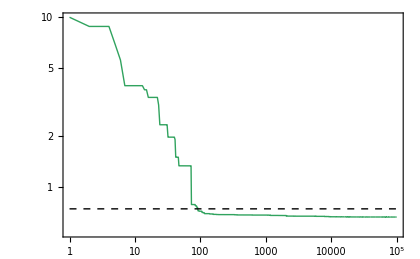

```mathematica
(* Plot of χ^2 over the generations *)
ListLogLogPlot[DataAccuracy//Abs,Joined->True,
PlotRange->{{1,10^5},All},PlotStyle->{Directive[Thick,RGBColor[0.1,0.6,0.3],Opacity[0.9]]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\text{Generations}","\\text{MAPE}(\\text{GA})"},RotateLabel->True,BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420,
Epilog->{{Dashed,Thick,Line[{{1,MAPE[TEHnw[k*h,h,ωb,ωm]]},{10^5,MAPE[TEHnw[k*h,h,ωb,ωm]]}}//Log]},Text[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{MAPE}(\\text{EH})"], Scaled[{0.7, 0.18}]]}]
```

## Evaluation

### Comparison

```mathematica
(* Best-Fit from the GA, the EH formula, and CLASS datapoints *)
LogLinearPlot[{Tnw[k,h,ωb,ωm],TEHnw[k*h,h,ωb,ωm]}/.h->NormPartData⟦10⟧⟦1,2⟧/.ωb->NormPartData⟦10⟧⟦1,3⟧/.ωm->NormPartData⟦10⟧⟦1,4⟧//Evaluate,{k,5*10^-6,5},PlotRange->All,PlotStyle->{Directive[Thick,Red],Directive[Thick,Dashed,LightBlue],,Directive[Thick,Dashed,Green]},
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Times",FontSize->16},Axes->False,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{GA Solution}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{EH Formula}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,10}],
{0.3,0.25}],ImageSize->420];
ListPlot[Table[{NormPartData⟦10⟧⟦i,1⟧,NormPartData⟦10⟧⟦i,5⟧},{i,1,Length[NormPartData⟦1⟧]}],Joined->False,PlotRange->{{NormPartData⟦10⟧⟦1,1⟧,NormPartData⟦10⟧⟦-1,1⟧},All},ScalingFunctions->{"Log","Linear"},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T(k)"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Black,PointSize[0.02]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{CLASS}"]}],
{0.28,0.47}],ImageSize->Medium];
Show[%,%%,ImageSize->420]
```

```mathematica
(* Fractional accuracy across scales *)
MAPEEH=Table[{NormPartData[[i]]⟦j,1⟧,100*Abs[(1-1/(NormPartData[[i]]⟦j,5⟧)TEHnw[NormPartData[[i]]⟦j,1⟧*NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,3⟧,NormPartData[[i]]⟦j,4⟧])]},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}];
MAPEGAs=Table[{NormPartData[[i]]⟦j,1⟧,100*Abs[(1-1/(NormPartData[[i]]⟦j,5⟧)(Tnw[NormPartData[[i]]⟦j,1⟧,NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,3⟧,NormPartData[[i]]⟦j,4⟧]))]},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}];
```

```mathematica
Table[Mean[MAPEEH[[i]][[All,2]]],{i,1,Length[MAPEEH]}]
{%//Mean,%//Min}
Table[Mean[MAPEGAs[[i]][[All,2]]],{i,1,Length[MAPEGAs]}]
{%//Mean,%//Min}
Position[%%,%%//Min] (* Best approximated dataset *)
```

{0.957233,0.957773,0.958162,0.958581,0.90541,0.905774,0.906255,0.90664,0.865046,0.865301,0.865517,0.865682,0.845464,0.846531,0.847723,0.848551,0.990229,0.990018,0.9902,0.99083,0.933401,0.934121,0.934586,0.935197,0.887912,0.887964,0.8882,0.888487,0.860725,0.861631,0.862591,0.863171,1.02672,1.02555,1.0252,1.02561,0.961576,0.962353,0.963184,0.964023,0.912186,0.912844,0.913566,0.914207,0.878503,0.87857,0.87882,0.879134,1.06522,1.06441,1.06388,1.06374,0.992468,0.992726,0.992757,0.993307,0.93735,0.93869,0.939689,0.940696,0.899051,0.899042,0.899277,0.899129}

{0.932944,0.845464}

{0.883365,0.884426,0.885414,0.886337,0.798922,0.799228,0.799463,0.799981,0.742209,0.741859,0.741896,0.742452,0.723127,0.722803,0.72267,0.723203,0.880095,0.878164,0.878935,0.879715,0.790626,0.789761,0.788957,0.788686,0.728042,0.72693,0.725999,0.726421,0.702578,0.702806,0.703148,0.703689,0.922004,0.920838,0.919401,0.91889,0.828876,0.829085,0.829061,0.828518,0.76347,0.764101,0.764455,0.764521,0.72755,0.728567,0.729123,0.729847,1.01657,1.0163,1.01522,1.01379,0.92485,0.92629,0.92784,0.928981,0.860829,0.861638,0.86221,0.86252,0.818485,0.819417,0.820037,0.820656}

{0.819623,0.702578}

{{29}}

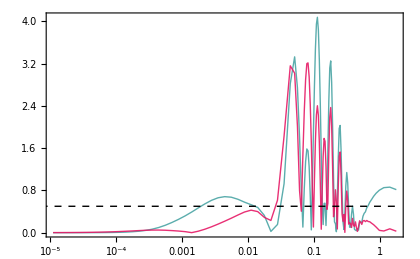

```mathematica
(* Comparison of accuracy for a given set *)
ListLogLinearPlot[{MAPEEH[[29]],MAPEGAs[[29]]},Joined->True,PlotRange->{{NormPartData⟦29⟧⟦1,1⟧,NormPartData⟦29⟧⟦-1,1⟧},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(k)"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0.2,0.6,0.6]],Directive[Thick,RGBColor[0.9,0.1,0.4],Opacity[0.9]],Directive[Thick,RGBColor[0.9,0.5,0.4],Opacity[0.9]]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{EH}"],(MaTeX[#,Magnification->1.5]&)/@Style["\\text{GAs}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],
{0.17,0.77}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],0.5},{Log[2],0.5}}]}},ImageSize->420]
```

### Savitzky-Golay Filter

```mathematica
(* Data from CLASS (python): {k, Subscript[T, SG](k)} *)
DataFilteredTk=Import["./Data/Filtered_Tk.txt","Data"]//Quiet;
ReducedDataTnwSG=Drop[Drop[Drop[DataFilteredTk,{1,-1,2}],{1,-1,2}],{1,-1,2}]//Quiet;
Length[ReducedDataTnwSG]/2500//N (* There are 16 lists *)
PartDataTnwSG=Partition[ReducedDataTnwSG,2500];
```

64.

```mathematica
TSG=ParallelTable[Interpolation[PartDataTnwSG[[i]]],{i,1,Length[PartDataTnwSG]}];
```

```mathematica
MAPESG=Table[{NormPartData[[i]]⟦j,1⟧,100*Abs[(1-(TSG[[i]][NormPartData[[i]]⟦j,1⟧])/(NormPartData[[i]]⟦j,5⟧))]},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}]//Quiet;
```

```mathematica
(* Mean fractional error across all cosmologies *)
Table[Mean[MAPESG[[i]][[All,2]]],{i,1,Length[accSG]}]//Quiet;
{Mean[#],Min[#]}&@%
Table[Mean[MAPEGAs[[i]][[All,2]]],{i,1,Length[MAPEGAs]}]//Quiet;
{Mean[#],Min[#]}&@%
Table[Mean[MAPEEH[[i]][[All,2]]],{i,1,Length[MAPEEH]}]//Quiet;
{Mean[#],Min[#]}&@%
```

{0.793347,0.656035}

{0.819623,0.702578}

{0.932944,0.845464}

## Test

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
LaunchKernels[];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
```

## Data

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
(* 200 spectra from a Latin-Hypercube of {h, Subscript[ω, b], Subscript[ω, m], Subscript[n, s], 10^9 Subscript[A, s], Subscript[σ, 8]} *)
dir="./Data/spectra_latin_hc/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## Fitting Functions

### Eisenstein-Hu: No-Wiggles

```mathematica
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
sh[ωb_,ωm_]:=(44.5*Log[9.83/ωm])/(√(1+10 ωb^(3/4))); (* Mpc *)
αΓ[ωb_,ωm_]:=1-0.328*Log[431*ωm]*ωb/ωm+0.38*Log[22.3*ωm]*(ωb/ωm)^2
Γeff[k_,h_,ωb_,ωm_]:=ωm/h(αΓ[ωb,ωm]+(1-αΓ[ωb,ωm])/(1+(0.43*k*sh[ωb,ωm])^4));
qeff[k_,h_,ωb_,ωm_]:=k/h*Θ^2/Γeff[k,h,ωb,ωm]; (* k in h/Mpc *)
L0eff[k_,h_,ωb_,ωm_]:=Log[2ⅇ+1.8*qeff[k,h,ωb,ωm]];
C0eff[k_,h_,ωb_,ωm_]:=14.2+731/(1+62.5*qeff[k,h,ωb,ωm]);
TEHnw[k_,h_,ωb_,ωm_]:=L0eff[k,h,ωb,ωm]/(L0eff[k,h,ωb,ωm]+C0eff[k,h,ωb,ωm]*qeff[k,h,ωb,ωm]^2)
```

### Genetic Algorithms

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)
```

```mathematica
{LeafCount[#],Depth[#]}&/@{Tnw[k,h,ωb,ωm],TEHnw[k*h,h,ωm,ωb]}
```

{{62,9},{378,20}}

## Comparison

### Compute Normalization

```mathematica
R8=8;            (* Mpc h^-1 *)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]); (* Top-hat Filter*)
σ8=Params[[All,6]];
```

```mathematica
IntegralEH[i_]:=NIntegrate[k^(Params[[i,4]]+2) TEHnw[k*Params[[i,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,100},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0EH=ParallelTable[2*π^2 σ8[[i]]^2/IntegralEH[i],{i,1,Length[Params]}];
```

```mathematica
MAPEEH[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-A0EH[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*TEHnw[PkData[[i]][[j,1]]*Params[[i,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2]},{j,Length[PkData[[i]]]}];
```

```mathematica
Table[Mean[MAPEEH[i][[All,2]]],{i,1,Length[Params]}];
{Min[#],Max[#],Position[#,Min[#]][[1,1]],Position[#,Max[#]][[1,1]]}&@%
{Mean[#],Median[#],Quantile[#,0.683],Quantile[#,0.955]}&@%%
```

{1.25095,1.94025,138,112}

{1.67816,1.73622,1.79523,1.88987}

```mathematica
IntegralGA[i_]:=NIntegrate[k^(Params[[i,4]]+2) Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GA=ParallelTable[2*π^2 σ8[[i]]^2/IntegralGA[i],{i,1,Length[Params]}];
```

```mathematica
MAPEGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-A0GA[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*Tnw[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2]},{j,Length[PkData[[i]]]}];
```

```mathematica
Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[Params]}];
{Min[#],Max[#],Position[#,Min[#]][[1,1]],Position[#,Max[#]][[1,1]]}&@%
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@%%
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[Params]}];
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[Params]}];
```

{0.767331,1.26768,2,153}

{0.991795,0.996028,1.06464,1.21145}

### Visual Comparison

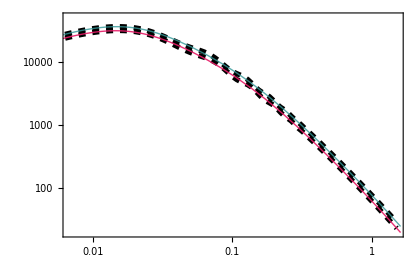

```mathematica
i=BestFit;j=WorstFit;
ListLogLogPlot[{PkData[[i]],PkData[[j]]},Joined->True,PlotRange->{{PkData[[1]][[110,1]],PkData[[1]][[-1,1]]},{20,5*10^4}},PlotStyle->{Directive[Thickness[0.009],Dashed,Black]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k) \\, [\\text{Mpc} \\, h^{-1}]^3 "},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
LogLogPlot[{A0GA[[i]]*k^Params[[i,4]]*Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2,
A0GA[[j]]*k^Params[[j,4]]*Tnw[k,Params[[j,1]],Params[[j,2]],Params[[j,3]]]^2}//Evaluate,{k,10^-5,1.6},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0.2,0.6,0.6]],Directive[Thick,RGBColor[0.9,0.1,0.4],Opacity[0.9]],Directive[Thick,RGBColor[0.3,0.6,0.2],Opacity[0.9]]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Best~fit}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Worst~fit}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],
{0.24,0.25}],ImageSize->420];
i=.;j=.;
Show[{%%%,%%}]
```

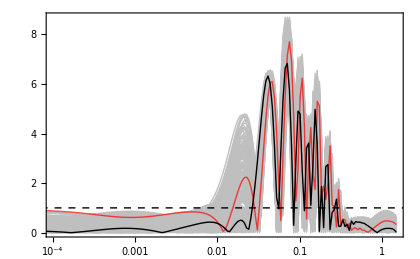

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[MAPEGA[i],{i,Select[Range[Length[Params]],#!=BestFit&&#!=WorstFit&]}],{MAPEGA[WorstFit],MAPEGA[BestFit]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Test set}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Worst fit}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},All},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k~[h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,14},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->420]//Quiet]
```

```mathematica
(* Relative Differences *)
RelDiffGA=Table[1-A0GA[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*Tnw[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2,{i,Length[Params]},{j,Length[PkData[[i]]]}];
(* k-values *)
ks=PkData[[1]][[All,1]];
(* Point-wise Percentile *)
percentiles=Quantile[Transpose[RelDiffGA],{0.5-0.34-0.136,0.5-0.34,0.5,0.5+0.34,0.5+0.34+0.136}];
{low2σ,low1σ,median,up1σ,up2σ}=Transpose[percentiles];
Show[ListLinePlot[{Transpose[{ks,low2σ}],Transpose[{ks,up2σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.890,0.102,0.110],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[{Transpose[{ks,low1σ}],Transpose[{ks,up1σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.121,0.466,0.705],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[Transpose[{ks,median}],PlotStyle->Directive[Black,Thick],PlotLegends->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[{{{Min[ks],0},{Max[ks],0}},{{Min[ks],0.01},{Max[ks],0.01}},{{Min[ks],-0.01},{Max[ks],-0.01}}},PlotStyle->{Directive[Dashed,Black]},Joined->True,ScalingFunctions->{"Log","Linear"},ImageSize->420],Epilog->{Inset[Framed[Column[{Row[{Graphics[{RGBColor[0.890,0.102,0.110],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["2\\sigma",Magnification->1.5]}],Row[{Graphics[{RGBColor[0.121,0.466,0.705],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["1\\sigma",Magnification->1.5]}]},Spacings->0.1],RoundingRadius->5,Background->White,FrameStyle->Black,FrameMargins->Small],Scaled[{0.14,0.17}]]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k~[h \\, \\mathrm{Mpc}^{-1}]",Magnification->1.5],MaTeX["\\Delta P_\\mathrm{lin}/P_\\mathrm{lin, True}",Magnification->1.5]},PlotRange->{{0.01,1.4}//Log,{-0.07,0.07}},BaseStyle->{FontFamily->"Times",FontSize->16}]
```

-Graphics-

# Full Transfer Function

```mathematica
Quit[]
```

## Data

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
Off[General::munfl];
Off[General::stop];
Off[Infinity::indet];
Off[Power::infy];
Off[Indeterminate::indet];
```

### Data

```mathematica
DataTransferFunction=Import["./Data/Transfer_Function_h_omegab_omegam.txt","Data"]//Quiet; (* Data from CLASS (python): {k, h, Subscript[ω, b], Subscript[ω, m], Φ} *)
Length[DataTransferFunction]/114//N (* There are 16 lists *)
PartData=Partition[DataTransferFunction,114]; (* Partition of data to consider each cosmology, i.e. each set {h, ωb, ωm}*)
(* Normalized data to get T(k) *)
NormPartData=Table[{#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,(#⟦5⟧)/Max[PartData⟦i,1,5⟧]}&/@PartData⟦i⟧,{i,1,Length[PartData]}]; 
MockData=Join@@NormPartData; (* Re-Join the datasets *)
Dimensions[MockData] (* Dimensions of the dataset *)
```

64.

{7296,5}

## Fitting Functions

## Genetic Algorithms

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)
```

## Genetic Algorithm

## Grammar, Fitness Function, and Genetic Instructions

### Grammar

```mathematica
(* Possible operations. The proposal grammar depends on each specific problem *)
poly[x_]:=x
grammar={poly}; (* Array of operations *)
```

### Genetic Code

```mathematica
(* Prior: *)
(* Subscript[T, w](k)= 1 + ((Subscript[α, b](Subscript[ω, b],Subscript[ω, m]))/(Subscript[rang, 2,1] + ((Subscript[β, b](Subscript[ω, b],Subscript[ω, m]))/ks)^Subscript[rang, 3,1])*ⅇ^(-(k/(Subscript[k, silk](Subscript[ω, b],Subscript[ω, m])))^Subscript[rang, 2,2]))*Sin[(Subscript[rang, 4,1] ks)/((Subscript[rang, 2,3] +((Subscript[β, node](Subscript[ω, m]))/ks)^Subscript[rang, 3,2])^Subscript[rang, 5,1])] *)
(* Subscript[α, b] = Subscript[rang, 5,2] + Subscript[rang, 6,1] Subscript[ω, b]^Subscript[rang, 5,3] + Subscript[rang, 5,4] Subscript[ω, m]^Subscript[rang, 2,4] *)
(* Subscript[β, b] = Subscript[rang, 7,1] + Subscript[rang, 8,1] Subscript[ω, b]^Subscript[rang, 2,5] + Subscript[rang, 9,1] Subscript[ω, m]^Subscript[rang, 2,6] *)
(* Subscript[β, node] = Subscript[rang, 10,1] Subscript[ω, m]^Subscript[rang, 5,5] *)
length=10; depth=10; (* Number of nucleotides and genes. Chromosomes will be 10x10 matrices *)
(* Ranges to compute random numbers specifying the expression of an individual *)
rang1={1,Length[grammar]}; (* To choose an operation in the grammar *)
rang2={0.5,1.5}; (* Look at the prior formula *)
rang3={0.5,3.5};
rang4={0.5,0.8};
rang5={0,1};
rang6={-0.5,0}; 
rang7={1,2}; 
rang8={-50,0};
rang9={0,60};
rang10={0.1,2};
```

### Fitness Function

```mathematica
(* Accuracy of an Individual -> MAPE% = 100|Subscript[f, GA] - Subscript[f, num]|/Subscript[f, num] *)
MAPEGA[f_]:=MAPEGA[f]=Module[{temp,ft},
ft=(f/.{x->#1,y->#2,z->#3,w->#4})&; (* Individual *)
temp=Mean[Table[1/MockData⟦i,5⟧Abs[MockData⟦i,5⟧-ft[MockData⟦i,1⟧,MockData⟦i,2⟧,MockData⟦i,3⟧,MockData⟦i,4⟧]]*100,{i,1,Length[MockData]}]]; (* Accuracy measure *)
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]] (* Space-Time constraints in the computation *)
```

## Genetic Operators

### Mutation

```mathematica
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{0,length}],RandomInteger[{0,depth}]}; (* To decide where apply a mutation *)
mut=Which[
rep⟦2⟧==1,RandomInteger[rang1], (* If rep⟦2⟧ == 1 -> modify the operation *)
rep⟦2⟧==2,RandomReal[rang2],
rep⟦2⟧==3,RandomReal[rang3], 
rep⟦2⟧==4,RandomReal[rang4],
rep⟦2⟧==5,RandomReal[rang5],
rep⟦2⟧==6,RandomReal[rang6],
rep⟦2⟧==7,RandomReal[rang7],
rep⟦2⟧==8,RandomReal[rang8], 
rep⟦2⟧==9,RandomReal[rang9], 
rep⟦2⟧==10,RandomReal[rang10]];
ReplacePart[kid,rep->mut]] (* Replace rep = {a, b} by mut = c in kid *)
```

### Crossover

```mathematica
cross[{kid1_,kid2_}]:=Module[{len},
len=RandomInteger[{1,length-1}]; (* Till length - 1 to not exceed the length of the chromosomes *)
{Join[kid1⟦1;;len⟧,kid2⟦(len+1);;-1⟧], (* Interchange of nucleotides *)
Join[kid1⟦(len+1);;-1⟧,kid2⟦1;;len⟧]}]
```

## Selection Scheme

### Tournament Selection

```mathematica
toursize=4; (* Participants in the tournament *)
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours], (* Take "tours" members from "fitnesses-set" at random *)
#1⟦1⟧>#2⟦1⟧&]⟦1,2⟧ (* Organize from greatest to smallest and take the individual with the best fit *)
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours], 
#1⟦1⟧>#2⟦1⟧&]⟦-1,2⟧ (* The same but taking the individual with the worst fit *)
```

## Genetic Algorithm

### Evolution of the Genetic Algorithm

```mathematica
(* Sound horizon expression from GAs [arXiv:2106.00428] *)
c1=0.00785436;c2=0.177084;c3=0.00912388;c4=0.618711;
c5=11.9611;c6=2.81343;c7=0.784719;
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
(* Diffusion scale from minimization process using CLASS data: *)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
selectionrate=0.3; (* Portion of the population to be sorted and replaced *)
(* Subscript[α, b] = Subscript[a, 10] + Subscript[a, 12] Subscript[ω, b]^Subscript[b, 10] + Subscript[a, 12] Subscript[ω, m]^Subscript[b, 11] *)
αbGA[y_,z_,kid_,gram_]:=Sum[ gram⟦kid⟦i,1⟧⟧@(kid⟦i+1,5⟧+kid⟦i,6⟧y^kid⟦i+2,5⟧+kid[[i+3,5]] z^kid⟦i+3,2⟧),{i,1,1}]
(* Subscript[β, b] = Subscript[b, 12] + Subscript[a, 13] Subscript[ω, b]^Subscript[b, 13] + Subscript[a, 14] Subscript[ω, m]^Subscript[b, 14] *)
βbGA[y_,z_,kid_,gram_]:=Sum[ gram⟦kid⟦i,1⟧⟧@(kid⟦i,7⟧+kid⟦i,8⟧y^kid⟦i+4,2⟧+kid[[i,9]] z^kid⟦i+5,2⟧),{i,1,1}]
(* Subscript[β, node] = Subscript[a, 15] Subscript[ω, m]^Subscript[b, 15] *)
βnodeGA[z_,kid_,gram_]:=Sum[ gram⟦kid⟦i,1⟧⟧@(kid⟦i,10⟧z^kid⟦i+4,5⟧),{i,1,1}]
(* Creator -> converts the chromosomes in "individuals": Subscript[T, nw](1+Subscript[α, b]/(Subscript[a, 1]+(Subscript[β, b]/ks)^Subscript[a, 2])ⅇ^(-(k/Subscript[k, Silk])^Subscript[a, 3]))Sin((Subscript[a, 4] ks + Subscript[a, 8] Subscript[ω, m]^a9)/((Subscript[a, 5]+(Subscript[β, node]/ks)^Subscript[a, 6])^Subscript[a, 7])) *)
funcGAs[x_,y_,z_,w_,kid_,gram_]:=Tnw[x,y,z,w](1+(αbGA[z,w,kid,gram]/(kid[[1,2]]+(βbGA[z,w,kid,gram]/(x*y*sGA[z,w]))^kid[[1,3]])*ⅇ^(-((x*y)/(kid[[7,2]]*kSilk[z,w]))^kid[[2,2]]))*Sin[(kid[[1,4]]*(x*y*sGA[z,w]+kid[[2,4]]*w^kid[[2,6]]))/((kid[[3,2]]+(βnodeGA[w,kid,gram]/(x*y*sGA[z,w]))^kid[[2,3]])^kid[[1,5]])]);
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2]; (* Around 1/3 of the population will be selected as the best *)
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={}; (* store: {fitness, individual, chromosome} *)
(* Progenitors -> Creation of "pop" chromosomes: 8 nucleotides for each gene and a total of 8 genes *)
chromosomes=Table[{RandomInteger[rang1],RandomReal[rang2],RandomReal[rang3],RandomReal[rang4],RandomReal[rang5],RandomReal[rang6],RandomReal[rang7],RandomReal[rang8],RandomReal[rang9],RandomReal[rang10]},{pop},{length}];
t1=AbsoluteTime[];
(* "pigs" is a "prior". It is computed for all pop. Its form depends on the problem *)
Do[
pigs=funcGAs[x,y,z,w,#,grammar]&/@chromosomes;
(* {-χ^2 for jth pig , counter j} sorted from the greatest to the smallest fitness *)
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[MAPEGA[pigs⟦j⟧],2,10^230],10^8,10^230],j},{j,1,Length[pigs]}],#1⟦1⟧>#2⟦1⟧&];
(* Append to bestfitperstep the greatest fitness, and its corresponding expression, and chromosomes *)
AppendTo[bestfitperstep,{fitness⟦1,1⟧,pigs⟦fitness⟦1,2⟧⟧,chromosomes⟦fitness⟦1,2⟧⟧}];
(* Selection of the best parents -> They are divided in pairs *)
p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];
(* Crossover of pairs *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes⟦p2⟦jj,1⟧⟧,chromosomes⟦p2⟦jj,2⟧⟧}], (* Worst are replaced by the children of the fittest *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];
(* Mutation *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes⟦p2⟦jj,1⟧⟧],mutation[chromosomes⟦p2⟦jj,2⟧⟧]}, (* Worst are replaced by fittest mutations *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];
Off[General::munfl];
Off[General::stop];
prog`int++,{maxgens}];
Off[General::munfl];
Off[General::stop];
If[verbose==True,
Print["Time taken: ",Round[AbsoluteTime[]-t1]," secs or ",Round[(AbsoluteTime[]-t1)/60], " mins"];
Print["MAPE = ",Abs[fitness⟦1,1⟧],"%"];
Print["Best-fit function is: "];
Print[bestfitperstep⟦-1,2⟧];
Speak["Finished..."];];
bestfitperstep]
```

## Evolution

### Several Random Seeds

```mathematica
(* We try with several random seeds *)
generations=100;
SaveState={};
samples=100;
prog`int=0;prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
t0=AbsoluteTime[];
Do[GApop1[j]=GAevo[1234j,generations,100,0.7,0.35,False]//Quiet;
Print["Time: ", AbsoluteTime[]-t0];
AppendTo[SaveState,{GApop1[j]⟦-1,1⟧,1234j}]; (* Save the accuracy and random seed *)
Export["Save_State_BAO.txt",SaveState,"Table"];
prog`pop++;prog`int=0;,{j,1,samples}];
```

Time: 70.860143

Time: 174.99867

Time: 292.63607

Time: 370.142873

Time: 446.988515

Time: 520.761201

Time: 623.371711

Time: 725.627428

Time: 803.531605

Time: 879.752822

Time: 957.098678

Time: 1070.42471

Time: 1163.17224

Time: 1238.67247

Time: 1316.68112

Time: 1396.46071

Time: 1497.218

Time: 1597.61478

Time: 1678.666

Time: 1758.3013

Time: 1838.55211

Time: 1941.79325

Time: 2050.37475

Time: 2133.902

Time: 2214.30965

Time: 2292.68465

Time: 2374.66533

Time: 2452.56325

Time: 2532.62575

Time: 2614.35826

Time: 2696.27703

Time: 2787.78428

Time: 2897.09365

Time: 2973.89494

Time: 3055.57674

Time: 3132.398

Time: 3248.73176

Time: 3338.21206

Time: 3417.81991

Time: 3495.09351

Time: 3572.65561

Time: 3653.294695

Time: 3734.141151

Time: 3817.221803

Time: 3895.013779

Time: 3973.774389

Time: 4043.439765

Time: 4133.647003

Time: 4214.425255

Time: 4292.379776

Time: 4380.076401

Time: 4480.405785

Time: 4556.933954

Time: 4634.637636

Time: 4717.254935

Time: 4792.160169

Time: 4913.917292

Time: 5000.041912

Time: 5078.739993

Time: 5160.067477

Time: 5236.550933

Time: 5317.654493

Time: 5394.869839

Time: 5473.816753

Time: 5549.033137

Time: 5621.029038

Time: 5697.213197

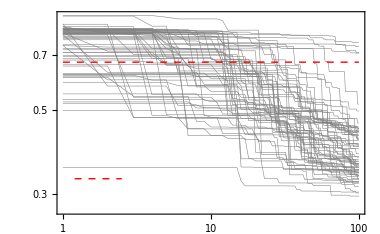

```mathematica
(* Plot the accuracy of GA solutions *)
Severalχ2=ListLogLogPlot[Table[GApop1[jj]⟦All,1⟧//Abs,{jj,1,67}],Joined->True,PlotRange->{{1,generations},All},Frame->True,PlotStyle->{Directive[Gray,Thickness[0.001]]},FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\chi^2"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->False,ImageSize->380,
Epilog->{{Dashed,Thick,Red,Line[{{1,0.67},{generations,0.67}}//Log]},{Dashed,Thick,Red,Line[{{1.2,0.33},{2.5,0.33}}//Log]},Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{No Wiggles}"], Scaled[{0.35, 0.15}]]}]
```

```mathematica
DataSaved=Import["Save_State_BAO.txt","Data"];
```

```mathematica
(* Best individual *)
Elite=Max[DataSaved⟦All,1⟧];
PosElite=Position[DataSaved,Elite];
DataSaved⟦PosElite⟦1,1⟧⟧ (* Determine the random seed and the accuracy of the winner *)
```

{-0.296972,64168}

### Long Run For the Winner

```mathematica
generations=1;
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, max generations, population, crossover-rate, mutation-rate, verbose (True/False)} *)
GApop=GAevo[64168,generations,100,0.7,0.35,True]//Quiet;(* Retrieve bestfitperstep = {fitness, expression, chromosomes} *)
```

Time taken: 6 secs or 0 mins

MAPE = 0.740854%

Best-fit function is:

(1+(ⅇ^(-1.47061 ((x y)/(0.195 w^1.0957+0.373 z^0.419))^0.651261) (0.353073+0.721003 w^1.46698-0.398082 z^0.261583) Sin[(0.637381 (0.635825/w^0.354179+(x y)/(0.00912388 w^0.618711+0.00785436 z^0.177084+11.9611 w^0.784719 z^2.81343)))/((0.514709+1.13284 ((w^0.757556 (0.00912388 w^0.618711+0.00785436 z^0.177084+11.9611 w^0.784719 z^2.81343))/(x y))^1.08965)^0.576762)])/(1.38449+(((1.59148+52.9774 w^0.514724-11.8633 z^1.2153) (0.00912388 w^0.618711+0.00785436 z^0.177084+11.9611 w^0.784719 z^2.81343))/(x y))^2.75447))/((1+101.855 ((x y)/(w-z))^1.483+21112.2 ((x y)/(w-z))^3.972+35913.1 ((x y)/(w-z))^6.097+1428.08 ((x y)/(w-z))^7.507)^(1/4))

```mathematica
(* Check the correct limits of the GA solution *)
GApop⟦-1,2⟧/.x->0//Quiet
Limit[GApop⟦-1,2⟧/.y->0.7/.z->0.022/.w->0.13,x->∞]
```

1.

0.

```mathematica
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;

b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 

Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]
```

```mathematica
(* Only if you want to run the GAs again and save the pointwise accuracy *)
(* Export["Generations_Accuracy_BAO.txt",Abs[GApop⟦All,1⟧],"Table"]; *)
```

```mathematica
{LeafCount[TGA[k,h,ωb,ωm]],Depth[TGA[k,h,ωb,ωm]]}
```

{214,14}

### Silk Correction

#### Accuracy

```mathematica
MAPEGAs=Table[{NormPartData[[i]]⟦j,1⟧,100*Abs[1-1/(NormPartData[[i]]⟦j,5⟧)(TGA[NormPartData[[i]]⟦j,1⟧,NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,3⟧,NormPartData[[i]]⟦j,4⟧])]},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}];
```

```mathematica
{Mean[#],Min[#],Max[#]}&@Table[Mean[MAPEGAs[[i]][[All,2]]],{i,1,Length[MAPEGAs]}]
```

{0.291587,0.220029,0.399864}

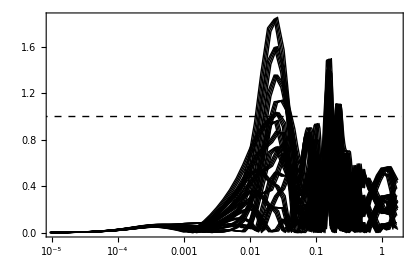

```mathematica
(* The ERROR of the GAs formula is in general below 1% for all scales *)
ListLogLinearPlot[Table[MAPEGAs[[i]],{i,1,Length[MAPEGAs]}],Joined->True,PlotRange->{{NormPartData⟦1⟧⟦1,1⟧,NormPartData⟦1⟧⟦-1,1⟧},All},PlotStyle->{Directive[Thin,Black]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Opacity[0.5]},Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->420]
(* There is a problematic peak around k = 0.01 h/Mpc *)
```

```mathematica
(* We add a correction for the amplitude supression due to photon difussion *)
TGAMin[x_,y_,z_,w_,A_,σ_,ks_]:=TGA[x,y,z,w](1+A*ⅇ^(-((x-ks)/σ)^2))
χ2WinnerMin[A_,σ_,ks_]:=Mean[ParallelTable[1/MockData⟦i,5⟧Abs[MockData⟦i,5⟧-TGAMin[MockData⟦i,1⟧,MockData⟦i,2⟧,MockData⟦i,3⟧,MockData⟦i,4⟧,A,σ,ks]]*100,{i,1,Length[MockData]}]];
FindMinimum[χ2WinnerMin[A,σ,ks],{{A,-0.06},{σ,0.06},{ks,0.19}},MaxIterations->1000,AccuracyGoal->10,PrecisionGoal->10]//Quiet
BestFit=%[[2]];
```

{0.250271,{A→-0.00624915,σ→0.0626709,ks→0.199448}}

## Evaluation

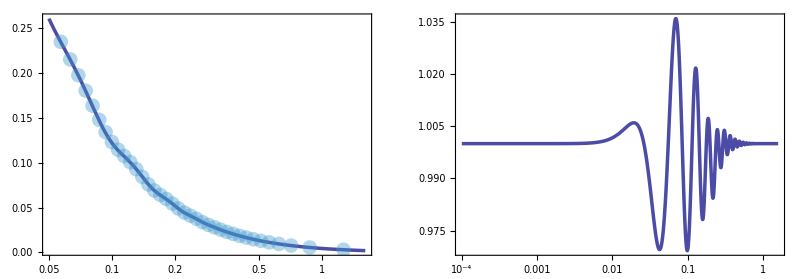

```mathematica
ListLogLinearPlot[Drop[Table[{NormPartData[[11]][[i,1]],NormPartData[[11]][[i,5]]},{i,40,114}],{1,-1,2}],PlotStyle->{Directive[PointSize[0.025],Opacity[0.4]]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\texttt{CLASS}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendMarkerSize->15],
{0.19,0.2}],ImageSize->420];
LogLinearPlot[TGAMin[x,y,z,w,A,σ,ks]/.BestFit/.y->NormPartData[[11]][[1,2]]/.z->NormPartData[[11]][[1,3]]/.w->NormPartData[[11]][[1,4]]//Evaluate,{x,5*10^-2,1.6},PlotRange->All,PlotStyle->{Directive[Thickness[0.006],RGBColor[0,0,0.5],Opacity[0.7]]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]"},
BaseStyle->{FontFamily->"Times",FontSize->16},Axes->False,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{GA Solution}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,10},LegendMarkerSize->{25,15}],
{0.22,0.1}],ImageSize->420];
Show[{%,%%},ImageSize->420];
LogLinearPlot[(TGAMin[x,y,z,w,A,σ,ks]/Tnw[x,y,z,w])/.BestFit/.y->NormPartData[[11]][[1,2]]/.z->NormPartData[[11]][[1,3]]/.w->NormPartData[[11]][[1,4]]//Evaluate,{x,10^-4,1.6},PlotRange->All,PlotStyle->{Directive[Thickness[0.006],RGBColor[0,0,0.5],Opacity[0.7]]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]"},
BaseStyle->{FontFamily->"Times",FontSize->16},Axes->False,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{GA Solution}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendMarkerSize->{25,15}],
{0.3,0.1}],ImageSize->420];
GraphicsRow[{%%,%},Frame->All,ImageSize->Full]
(* Left: Zoom of the fit where BAOs are found. Right: BAOs signal. *)
```

#### Accuracy

```mathematica
MAPEGA=Table[{NormPartData[[i]]⟦j,1⟧,100*Abs[(1-1/(NormPartData[[i]]⟦j,5⟧)(TGAMin[NormPartData[[i]]⟦j,1⟧,NormPartData[[i]]⟦j,2⟧,NormPartData[[i]]⟦j,3⟧,NormPartData[[i]]⟦j,4⟧,A,σ,ks])/.BestFit)]},{i,1,Length[NormPartData]},{j,1,Length[NormPartData[[i]]]}];
```

```mathematica
Table[Mean[MAPEGA[[i]][[All,2]]],{i,1,Length[MAPEGA]}]
{%//Mean,%//Min}
```

{0.374846,0.37921,0.383214,0.387884,0.287276,0.291989,0.29741,0.302403,0.253676,0.260291,0.266001,0.271234,0.269563,0.272582,0.277902,0.283322,0.290343,0.290825,0.29533,0.300605,0.198266,0.198065,0.200622,0.204771,0.169588,0.162487,0.161987,0.165127,0.206874,0.199536,0.194214,0.192257,0.273074,0.271244,0.271555,0.272357,0.191441,0.184745,0.181506,0.180199,0.160517,0.155432,0.150408,0.145136,0.214745,0.210052,0.205797,0.203392,0.349419,0.346377,0.345056,0.344528,0.270651,0.267594,0.264731,0.262723,0.221196,0.218966,0.21712,0.21623,0.286176,0.283196,0.281567,0.280493}

{0.250271,0.145136}

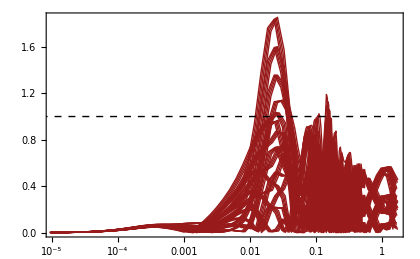

```mathematica
(* The accuracy of the GAs formula is in general below 1% for all scales *)
ListLogLinearPlot[Table[MAPEGAs[[i]],{i,1,Length[MAPEGAs]}],Joined->True,PlotRange->{{NormPartData⟦1⟧⟦1,1⟧,NormPartData⟦1⟧⟦-1,1⟧},All},PlotStyle->{Directive[Thin,RGBColor[0.6,0.1,0.1]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Opacity[0.5]},Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->420]
(* There is a problematic peak around k = 0.01 h/Mpc *)
```

## Test

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
LaunchKernels[];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
```

## Data

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
(* 200 spectra from latin-hypercube {h, Subscript[ω, b], Subscript[ω, m], Subscript[n, s], 10^9 Subscript[A, s]} *)
dir="./Data/spectra_latin_hc/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## Fitting Function

### Eisenstein-Hu: No-Wiggles

```mathematica
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
sEH[ωb_,ωm_]:=(44.5*Log[9.83/ωm])/(√(1+10 ωb^(3/4))); (* Mpc *)
αΓ[ωb_,ωm_]:=1-0.328*Log[431*ωm]*ωb/ωm+0.38*Log[22.3*ωm]*(ωb/ωm)^2
Γeff[k_,h_,ωb_,ωm_]:=ωm/h(αΓ[ωb,ωm]+(1-αΓ[ωb,ωm])/(1+(0.43*k*sEH[ωb,ωm])^4));
qeff[k_,h_,ωb_,ωm_]:=k/h*Θ^2/Γeff[k,h,ωb,ωm]; (* k in h/Mpc *)
L0eff[k_,h_,ωb_,ωm_]:=Log[2ⅇ+1.8*qeff[k,h,ωb,ωm]];
C0eff[k_,h_,ωb_,ωm_]:=14.2+731/(1+62.5*qeff[k,h,ωb,ωm]);
TEHnw[k_,h_,ωb_,ωm_]:=L0eff[k,h,ωb,ωm]/(L0eff[k,h,ωb,ωm]+C0eff[k,h,ωb,ωm]*qeff[k,h,ωb,ωm]^2)
```

### Eisenstein-Hu

```mathematica
(* All the formulas are extracted from EH97I[9709112 v1] paper,unless stated. *)
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
(* See Eq. (11) *)
a1EH[ωm_]:=(46.9ωm)^0.670 (1+(32.1 ωm)^-0.532)
a2EH[ωm_]:=(12.0 ωm)^0.424 (1+(45.0 ωm)^-0.582) 
αc[ωb_,ωm_]:=a1EH[ωm]^(-ωb/ωm)*a2EH[ωm]^(-(ωb/ωm)^3)
(* See Eq. (12) *)
b1EH[ωm_] := 0.944 (1+(458 ωm)^-0.708)^-1 
b2EH[ωm_]:=(0.395 ωm)^-0.0266 
βc[ωb_,ωm_]:=(1+b1EH[ωm](((ωm - ωb)/ωm)^b2EH[ωm]-1))^-1 
(* Redshift at drag epoch -> See Eq. (4) *)
b1d[ωm_]:=0.313 ωm^-0.419 (1 + 0.607 ωm^0.674) 
b2d[ωm_]:=0.238 ωm^0.223 
zd[ωb_,ωm_]:=1291*ωm^0.251/(1 + 0.659 ωm^0.828)(1 + b1d[ωm] ωb^b2d[ωm]) 
zeqEH[ωm_]:=2.5*10^4 ωm*Θ^-4 (* Redshift at equilibrium epoch -> See Eq. (2) *)
keqEH[ωm_]:=7.46*10^-2 ωm*Θ^-2  (* scale at equilibrium epoch -> See Eq. (3) *)
qEH[k_,ωm_] := k/(13.41 keqEH[ωm])  (* See Eq. (10) *)
REH[z_,ωb_]:=31.5*ωb*Θ^-4*(z/10^3)^-1  (* Baryon-Photon ratio -> See Eq. (5) *)
yEH[z_,ωm_]:=(1+zeqEH[ωm])/(1+z) (* Useful variable for calculations in LS limit -> See Eq.(8.20) in Dodelson 2 *)
(* Sub-horizon solution of the Mezsaros' eq. -> See Eq. (8.63) in Dodelson 2 *)
GEH[z_,ωm_]:=yEH[z, ωm] (-6 √(1+yEH[z,ωm])+(2+3yEH[z,ωm])Log[(√(1 + yEH[z, ωm])+1)/(√(1 + yEH[z, ωm])-1)]) 
(* Silk damping scale -> See Eq. (7) *)
kSilkEH[ωb_,ωm_]:=1.6 ωb^0.52*ωm^0.73(1+(10.4 ωm)^-0.95) (* [(Mpc^-1)]*)
βnode[ωm_]:=8.41*ωm^0.435 (* Shifting of nodes parameter -> See Eq. (23) *)
st[k_,ωb_,ωm_]:=sEH[ωb,ωm]/((1+(βnode[ωm]/(k*sEH[ωb, ωm]))^3)^(1/3)) (* Shifting of oscillations nodes -> See Eq. (22) *)
(* Amplitude of small scale contributions -> See Eq. (14) *)
αb[ωb_,ωm_]:=2.07*keqEH[ωm]*sEH[ωb,ωm] (1+REH[zd[ωb,ωm],ωb])^(-3/4)GEH[yEH[zd[ωb,ωm],ωm], ωm] 

(* Small scale contributions -> See Eq. (24) *)
βb[ωb_,ωm_]:=0.5+ωb/ωm+(3-2 ωb/ωm) √((17.2 ωm)^2+1)
fEH[k_,ωb_,ωm_]:=1/(1 + ((k*sEH[ωb, ωm])/5.4)^4) (* See Eq (18) *)
Cf[k_,ωb_,ωm_]:=14.2/αc[ωb,ωm]+386/(1 + 69.9*qEH[k,ωm]^1.08) (* See Eq. (20) *)
Cfαc1[k_,ωb_,ωm_]:=14.2 + 386/(1 + 69.9*qEH[k,ωm]^1.08) (* Cf with αc = 1*)
(* See Eq. (19) *)
T0[k_,ωb_,ωm_]:=Log[ⅇ + 1.8*βc[ωb,ωm]*qEH[k,ωm]]/(Log[ⅇ+1.8 βc[ωb,ωm]*qEH[k,ωm]]+Cf[k,ωb,ωm]*qEH[k,ωm]^2)
(* See Eqs. (19) and (20) in EH97: T0(k, 1, βc) means αc = 1 in Eq. (20) *)
T01[k_,ωb_,ωm_]:=Log[ⅇ+1.8*βc[ωb,ωm]*qEH[k,ωm]]/(Log[ⅇ + 1.8 βc[ωb,ωm]*qEH[k,ωm]]+Cfαc1[k,ωb,ωm]*qEH[k,ωm]^2)
(* See Eq. (19) in EH97: T0(k, 1, 1) means αc = 1 in Eq. (20) and βc = 1 in Eq. (19) *)
T011[k_,ωb_,ωm_]:=Log[ⅇ+1.8*qEH[k,ωm]]/(Log[ⅇ+1.8*qEH[k,ωm]]+Cfαc1[k,ωb,ωm]*qEH[k,ωm]^2)
(* Transfer function for CDM -> See Eq. (17) *)
TcEH[k_,ωb_,ωm_]:=fEH[k,ωb,ωm]*T01[k,ωb,ωm]+(1-fEH[k,ωb,ωm])T0[k,ωb,ωm]
(* Transfer function for baryons -> See Eq. (21) *)
TbEH[k_,ωb_,ωm_]:=(T011[k, ωb, ωm]/(1+((k*sEH[ωb,ωm])/5.2)^2)+αb[ωb,ωm]/(1 + (βb[ωb,ωm]/(k*sEH[ωb,ωm]))^3)ⅇ^(-(k/kSilkEH[ωb,ωm])^1.4))Sin[k*st[k,ωb,ωm]]/(k*st[k,ωb,ωm])
(* Transfer function for CDM + baryons -> See Eq. (16) *)
TEH[k_,ωb_,ωm_] := (ωm - ωb)/ωm TcEH[k,ωb,ωm]+ωb/ωm TbEH[k,ωb,ωm]
```

### Genetic Algorithms

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]
```

```mathematica
{LeafCount[#],Depth[#]}&/@{TGA[k,h,ωb,ωm],TEH[k*h,ωm,ωb]}
```

{{227,14},{1039,25}}

## Comparison

### Compute Normalization

```mathematica
R8=8;            (* Mpc h^-1 *)
(* Top-hat Filter*)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]);
σ8=Params[[All,6]];
```

```mathematica
IntegralEH[i_]:=NIntegrate[k^(Params[[i,4]]+2) TEHnw[k*Params[[i,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,10},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0EH=ParallelTable[2*π^2 σ8[[i]]^2/IntegralEH[i],{i,1,Length[Params]}];
```

```mathematica
MAPEEH[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-A0EH[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*TEH[PkData[[i]][[j,1]]*Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2]},{j,Length[PkData[[i]]]}];
```

```mathematica
ParallelTable[Mean[MAPEEH[i][[All,2]]],{i,1,Length[Params]}];
{Min[#],Max[#],Position[#,Min[#]][[1,1]],Position[#,Max[#]][[1,1]]}&@%
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@%%
```

{1.34001,1.92879,117,112}

{1.6298,1.62578,1.71143,1.83744}

```mathematica
IntegralGA[i_]:=NIntegrate[k^(Params[[i,4]]+2) Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GA=Table[2*π^2 σ8[[i]]^2/IntegralGA[i],{i,1,Length[Params]}];
```

```mathematica
MAPEGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-A0GA[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*TGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2]},{j,Length[PkData[[i]]]}];
```

```mathematica
Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[Params]}];
{Min[#],Max[#],Position[#,Min[#]][[1,1]],Position[#,Max[#]][[1,1]]}&@%
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@%%
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[Params]}];
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[Params]}];
```

{0.18684,0.679159,69,153}

{0.422813,0.427701,0.478041,0.623092}

### Visual Comparison

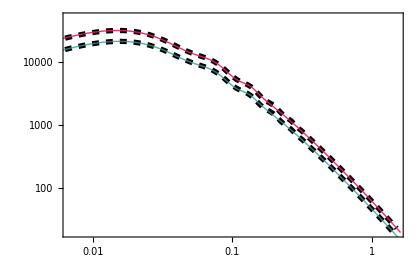

```mathematica
i=BestFit;j=WorstFit;
ListLogLogPlot[{PkData[[i]],PkData[[j]]},Joined->True,PlotRange->{{PkData[[1]][[110,1]],PkData[[1]][[-1,1]]},{20,5*10^4}},PlotStyle->{Directive[Thickness[0.009],Dashed,Black]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k) \\, [\\text{Mpc} h^{-1}]^3 "},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
LogLogPlot[{A0GA[[i]]*k^Params[[i,4]]*TGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2,
A0GA[[j]]*k^Params[[j,4]]*TGA[k,Params[[j,1]],Params[[j,2]],Params[[j,3]]]^2}//Evaluate,{k,10^-5,1.6},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0.2,0.6,0.6]],Directive[Thick,RGBColor[0.9,0.1,0.4],Opacity[0.9]],Directive[Thick,RGBColor[0.3,0.6,0.2],Opacity[0.9]]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Best~fit}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Worst~fit}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],
{0.23,0.24}],ImageSize->420];
i=.;j=.;
Show[{%%%,%%}]
```

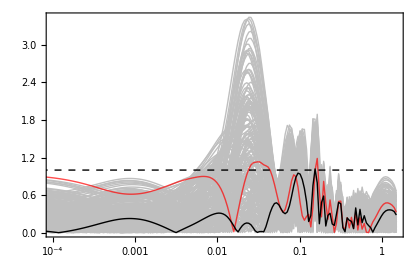

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[MAPEGA[i],{i,Select[Range[Length[Params]],#!=BestFit&&#!=WorstFit&]}],{MAPEGA[WorstFit],MAPEGA[BestFit]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Test set}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Worst fit}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},All},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,14},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->420]//Quiet]
```

```mathematica
(* Relative Differences *)
RelDiffGA=Table[1-A0GA[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*TGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2,{i,Length[Params]},{j,Length[PkData[[i]]]}];
(* k-values *)
ks=PkData[[1]][[All,1]];
(* Point-wise Percentile *)
percentiles=Quantile[Transpose[RelDiffGA],{0.5-0.34-0.136,0.5-0.34,0.5,0.5+0.34,0.5+0.34+0.136}];
{low2σ,low1σ,median,up1σ,up2σ}=Transpose[percentiles];
Show[ListLinePlot[{Transpose[{ks,low2σ}],Transpose[{ks,up2σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.890,0.102,0.110],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[{Transpose[{ks,low1σ}],Transpose[{ks,up1σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.121,0.466,0.705],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[Transpose[{ks,median}],PlotStyle->Directive[Black,Thick],PlotLegends->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[{{{Min[ks],0},{Max[ks],0}},{{Min[ks],0.01},{Max[ks],0.01}},{{Min[ks],-0.01},{Max[ks],-0.01}}},PlotStyle->{Directive[Dashed,Black]},Joined->True,ScalingFunctions->{"Log","Linear"},ImageSize->420],Epilog->{Inset[Framed[Column[{Row[{Graphics[{RGBColor[0.890,0.102,0.110],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["2\\sigma",Magnification->1.5]}],Row[{Graphics[{RGBColor[0.121,0.466,0.705],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["1\\sigma",Magnification->1.5]}]},Spacings->0.1],RoundingRadius->5,Background->White,FrameStyle->Black,FrameMargins->Small],Scaled[{0.14,0.17}]]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k~[h \\, \\mathrm{Mpc}^{-1}]",Magnification->1.5],MaTeX["\\Delta P_\\mathrm{lin}/P_\\mathrm{lin, True}",Magnification->1.5]},PlotRange->{{0.01,1.4}//Log,{-0.02,0.035}},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLabel->MaTeX["\\text{No~Corrections~around}~k_\\text{Silk}",Magnification->1.5]]
```

-Graphics-

### Silk Correction

```mathematica
MockData=Drop[Drop[Join@@Table[{PkData[[j]][[i,1]],Params[[j,1]],Params[[j,2]],Params[[j,3]],Params[[j,4]],A0GA[[j]],PkData[[j]][[i,2]]},{j,Length[PkData]},{i,Length[PkData[[j]]]}],{1,-1,2}],{1,-1,2}];
```

```mathematica
(* We add a correction for the amplitude supression due to photon difussion *)
PGAsMin[k_,h_,ωb_,ωm_,ns_,A0_,A_,σs_,ks_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2(1+A*ⅇ^(-((k-ks)/σs)^2))
χ2WinnerMin[A_,σs_,ks_]:=Mean[Table[Abs[1-1/MockData⟦i,7⟧PGAsMin[MockData⟦i,1⟧,MockData[[i,2]],MockData[[i,3]],MockData[[i,4]],MockData[[i,5]],MockData[[i,6]],A,σs,ks]]*100,{i,1,Length[MockData]}]];
```

```mathematica
ks=.;
χ2WinnerMin[0,σs,ks]
```

0.417195

```mathematica
FindMinimum[χ2WinnerMin[A,σs,ks],{{A,0.008},{σs,0.04},{ks,0.08}},MaxIterations->1000,AccuracyGoal->6,PrecisionGoal->6]//Quiet
```

{0.38789,{A→0.00897531,σs→0.0361638,ks→0.0796}}

```mathematica
PSilkPeak2[k_]:=(1+A*ⅇ^(-((k-ks)/σs)^2))/.{A->0.008975311298748994,σs->0.036163796196812134,ks->0.07959999300555506}
```

```mathematica
(* We add a correction for the amplitude supression due to photon difussion *)
PGAsMin[k_,h_,ωb_,ωm_,ns_,A0_,A_,σs_,ks_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2(1+A*ⅇ^(-((k-ks)/σs)^2))*PSilkPeak2[k];
χ2WinnerMin[A_,σs_,ks_]:=Mean[Table[Abs[1-1/MockData⟦i,7⟧PGAsMin[MockData⟦i,1⟧,MockData[[i,2]],MockData[[i,3]],MockData[[i,4]],MockData[[i,5]],MockData[[i,6]],A,σs,ks]]*100,{i,1,Length[MockData]}]]//Quiet;
```

```mathematica
FindMinimum[χ2WinnerMin[A,σs,ks],{{A,-0.01},{σs,0.005},{ks,0.15}},MaxIterations->100,AccuracyGoal->6,PrecisionGoal->6]//Quiet
```

{0.383594,{A→-0.0101979,σs→0.00849009,ks→0.143264}}

```mathematica
PSilkPeak3[k_]:=(1+A*ⅇ^(-((k-ks)/σs)^2))/.{A->-0.010197872440257504,σs->0.00849008710841401,ks->0.14326377417160635}
```

```mathematica
(* We add a correction for the amplitude supression due to photon difussion *)
PGAsMin[k_,h_,ωb_,ωm_,ns_,A0_,A_,σs_,ks_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2(1+A*ⅇ^(-((k-ks)/σs)^2))*PSilkPeak2[k]*PSilkPeak3[k];
χ2WinnerMin[A_,σs_,ks_]:=Mean[Table[Abs[1-1/MockData⟦i,7⟧PGAsMin[MockData⟦i,1⟧,MockData[[i,2]],MockData[[i,3]],MockData[[i,4]],MockData[[i,5]],MockData[[i,6]],A,σs,ks]]*100,{i,1,Length[MockData]}]]//Quiet;
```

```mathematica
FindMinimum[χ2WinnerMin[A,σs,ks],{{A,-0.001},{σs,0.5},{ks,1.1}},MaxIterations->100,AccuracyGoal->6,PrecisionGoal->6]//Quiet
```

{0.377034,{A→-0.00379213,σs→0.318533,ks→1.20114}}

```mathematica
PSilkPeak4[k_]:=(1+A*ⅇ^(-((k-ks)/σs)^2))/.{A->-0.003792128557335714,σs->0.31853323949655243,ks->1.2011357625616716}
```

```mathematica
MAPEGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-A0GA[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*TGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2*PSilkPeak2[PkData[[i]][[j,1]]]*PSilkPeak3[PkData[[i]][[j,1]]]*PSilkPeak4[PkData[[i]][[j,1]]]]},{j,Length[PkData[[i]]]}];
```

```mathematica
Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet;
{Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@%
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@%%
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet;
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet;
```

{0.14097,0.634882,{{177}},{{86}}}

{0.382033,0.378226,0.444324,0.567787}

### Visual Comparison

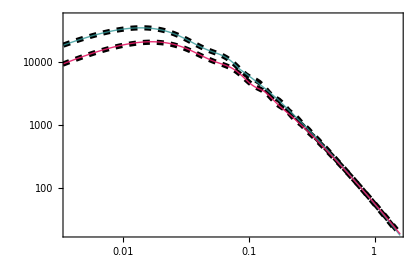

```mathematica
i=BestFit;j=WorstFit;
ListLogLogPlot[{PkData[[i]],PkData[[j]]},Joined->True,PlotRange->{{PkData[[1]][[100,1]],PkData[[1]][[-1,1]]},{20,5*10^4}},PlotStyle->{Directive[Thickness[0.009],Dashed,Black]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k) \\, [\\text{Mpc}\\,h^{-1}]^3 "},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
LogLogPlot[{A0GA[[i]]*k^Params[[i,4]]*TGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2*PSilkPeak2[k]*PSilkPeak3[k],
A0GA[[j]]*k^Params[[j,4]]*TGA[k,Params[[j,1]],Params[[j,2]],Params[[j,3]]]^2*PSilkPeak2[k]*PSilkPeak3[k]}//Evaluate,{k,10^-5,1.6},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0.2,0.6,0.6]],Directive[Thick,RGBColor[0.9,0.1,0.4],Opacity[0.9]],Directive[Thick,RGBColor[0.3,0.6,0.2],Opacity[0.9]]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Best~fit}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Worst~fit}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],
{0.23,0.25}],ImageSize->420];
i=.;j=.;
Show[{%%%,%%},ImageSize->420]
```

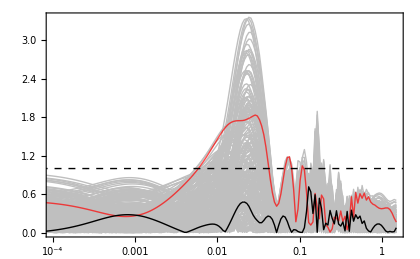

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[MAPEGA[i],{i,Select[Range[Length[Params]],#!=BestFit&&#!=WorstFit&]}],{MAPEGA[WorstFit],MAPEGA[BestFit]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Test set}"],(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},All},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k~[h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->420]//Quiet]//Quiet
```

```mathematica
(* Relative Differences *)
RelDiffGA=Table[1-A0GA[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*TGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2*PSilkPeak2[PkData[[i]][[j,1]]]*PSilkPeak3[PkData[[i]][[j,1]]]*PSilkPeak4[PkData[[i]][[j,1]]],{i,Length[Params]},{j,Length[PkData[[i]]]}]//Quiet;
(* k-values *)
ks=PkData[[1]][[All,1]];
(* Point-wise Percentile *)
percentiles=Quantile[Transpose[RelDiffGA],{0.5-0.34-0.136,0.5-0.34,0.5,0.5+0.34,0.5+0.34+0.136}];
{low2σ,low1σ,median,up1σ,up2σ}=Transpose[percentiles];
Show[ListLinePlot[{Transpose[{ks,low2σ}],Transpose[{ks,up2σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.890,0.102,0.110],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[{Transpose[{ks,low1σ}],Transpose[{ks,up1σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.121,0.466,0.705],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[Transpose[{ks,median}],PlotStyle->Directive[Black,Thick],PlotLegends->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[{{{Min[ks],0},{Max[ks],0}},{{Min[ks],0.01},{Max[ks],0.01}},{{Min[ks],-0.01},{Max[ks],-0.01}}},PlotStyle->{Directive[Dashed,Black]},Joined->True,ScalingFunctions->{"Log","Linear"},ImageSize->420],Epilog->{Inset[Framed[Column[{Row[{Graphics[{RGBColor[0.890,0.102,0.110],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["2\\sigma",Magnification->1.5]}],Row[{Graphics[{RGBColor[0.121,0.466,0.705],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["1\\sigma",Magnification->1.5]}]},Spacings->0.1],RoundingRadius->5,Background->White,FrameStyle->Black,FrameMargins->Small],Scaled[{0.14,0.17}]]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k~[h \\, \\mathrm{Mpc}^{-1}]",Magnification->1.5],MaTeX["\\Delta P_\\mathrm{lin}/P_\\mathrm{lin, True}",Magnification->1.5]},PlotRange->{{0.01,1.4}//Log,{-0.02,0.035}},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLabel->MaTeX["\\text{Corrections~around}~k_\\text{Silk}",Magnification->1.5]]//Quiet
```

-Graphics-

## Correction at k_eq

```mathematica
Quit[]
```

## Error on k_eq

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[];
Off[General::munfl];
Off[General::stop];
Off[Infinity::indet];
Off[Power::infy];
Off[Indeterminate::indet];
```

### Data

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
dir="./Data/spectra_latin_hc/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

### Fitting

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]
PGA[k_,h_,ωb_,ωm_,ns_,A_]:=A*k^ns*TGA[k,h,ωb,ωm]^2
```

```mathematica
R8=8;            (* Mpc h^-1 *)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]);(* Top-hat Filter *)
σ8=Params[[All,6]];
IntegralGA[i_]:=NIntegrate[k^(Params[[i,4]]+2) Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
(* Normalization factor *)
A0GA=ParallelTable[2*π^2 σ8[[i]]^2/IntegralGA[i],{i,1,Length[Params]}];
```

```mathematica
(* Normalization factor from MAPE minimization *)
MAPEGA[A_,i_]:=Mean[Table[100*Abs[1-PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A]/(PkData[[i]][[j,2]])],{j,Length[PkData[[i]]]}]];
FindAGA=Table[FindMinimum[MAPEGA[A,i],{A,10^6,10^7}],{i,Length[PkData]}]//Quiet;
AGA=FindAGA[[All,2,1,2]];
```

```mathematica
(* Search the maximum of Subscript[P, GA](k) *)kmaxGA=ParallelTable[FindMaximum[{PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]],k>10^-2&&k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[2,1,2]],{i,1,Length[PkData]}];
```

```mathematica
(* Interpolate CLASS and search the maximum *)
Pclass=ParallelTable[Interpolation[PkData[[i]]],{i,1,Length[PkData]}];
kmaxclass=ParallelTable[FindMaximum[{Pclass[[i]][k],k>10^-3&&k<1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[2,1,2]],{i,1,Length[Pclass]}];
```

```mathematica
(* Residuals in Subscript[k, max] *)
Δkmax=kmaxclass-kmaxGA;
Δkf=Abs[Δkmax]/kmaxclass*100;
```

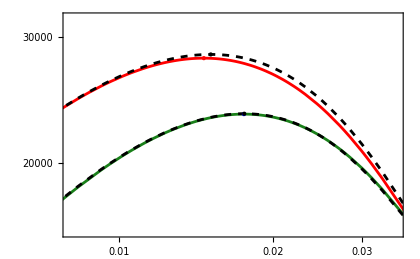

```mathematica
i=7;j=10;
Show[LogLogPlot[{PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]],
PGA[k,Params[[j,1]],Params[[j,2]],Params[[j,3]],Params[[j,4]],A0GA[[j]]],
Pclass[[i]][k],
Pclass[[j]][k]},{k,10^-4,1.5},PlotRange->{{0.008,0.035},{1.6*10^4,3.2*10^4}},PlotStyle->{Directive[RGBColor[0.1,0.5,0.1]],Directive[Red],Directive[Black,Dashed],Directive[Black,Dashed]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Best fit}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Worst fit}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],
{0.5,0.14}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k) \\, [(\\text{Mpc}\\,h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420],Graphics[{PointSize[Large],Blue,Point[{kmaxGA[[i]],PGA[kmaxGA[[i]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]}//Log],Red,Point[{kmaxGA[[j]],PGA[kmaxGA[[j]],Params[[j,1]],Params[[j,2]],Params[[j,3]],Params[[j,4]],A0GA[[j]]]}//Log],Black,Point[{kmaxclass[[i]],Pclass[[i]][kmaxclass[[i]]]}//Log],
Black,Point[{kmaxclass[[j]],Pclass[[j]][kmaxclass[[j]]]}//Log]}]]
i=.;j=.;
```

```mathematica
ΔAmp=Table[Abs[1-PGA[kmaxGA[[i]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]/(Pclass[[i]][kmaxclass[[i]]])]*100,{i,1,Length[PkData]}];
```

```mathematica
{ΔAmp[[7]],ΔAmp[[10]]}
{Δkf[[7]],Δkf[[10]]}
```

{0.129117,1.19579}

{0.157498,3.06391}

## Formulae: k_max,R(k_max),D(k_max)

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
dir="./Data/Spectra_kmax";
```

### k_eq

#### Varying h

```mathematica
(* Load, interpolate and find the {k,P(k)} at the maximum for each h*)
MaxPkh=Table[spectrum=Import[FileNameJoin[{dir,"spectrum_h_"<>ToString[i]<>".txt"}],"Table"];
Pk=Interpolation[spectrum];
FindMaximum[{Pk[k],10^-3<k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6],{i,0,3}];
```

```mathematica
(* Extract values of Subscript[k, max] and P(Subscript[k, max]) *)
hvals={0.65,0.683,0.716,0.75}
Pkmaxh=MaxPkh[[All,1]]
kmaxh=MaxPkh[[All,2,1,2]]
```

{0.65,0.683,0.716,0.75}

{19351.8,19610.1,19870.1,20131.4}

{0.0149897,0.0148941,0.0148004,0.0147075}

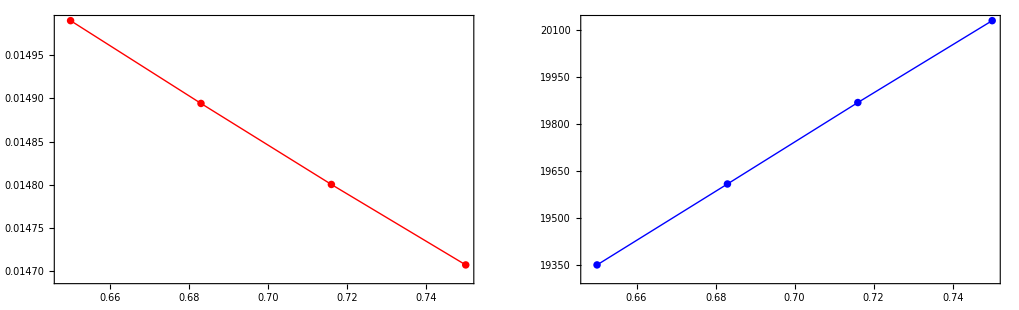

```mathematica
ListPlot[Transpose[{hvals,kmaxh}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"h","k_\\text{max}"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
ListPlot[Transpose[{hvals,Pkmaxh}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Blue]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"h","P(k_\\text{max})"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
GraphicsRow[{%%,%},ImageSize->1020]
```

#### Varying ω_b

```mathematica
(* Load, interpolate and find the {k,P(k)} at the maximum for each Subscript[ω, b] *)MaxPkωb=Table[spectrum=Import[FileNameJoin[{dir,"spectrum_omega_b_"<>ToString[i]<>".txt"}],"Table"];
Pk=Interpolation[spectrum];
FindMaximum[{Pk[k],10^-3<k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6],{i,0,3}];
```

```mathematica
(* Extract values of Subscript[k, eq] and P(Subscript[k, eq]) *)
ωbvals={0.0214,0.02206667,0.02273333,0.0234}
Pkmaxωb=MaxPkωb[[All,1]]
kmaxωb=MaxPkωb[[All,2,1,2]]
```

{0.0214,0.0220667,0.0227333,0.0234}

{19351.8,19349.7,19347.6,19345.7}

{0.0149897,0.0149847,0.0149794,0.0149746}

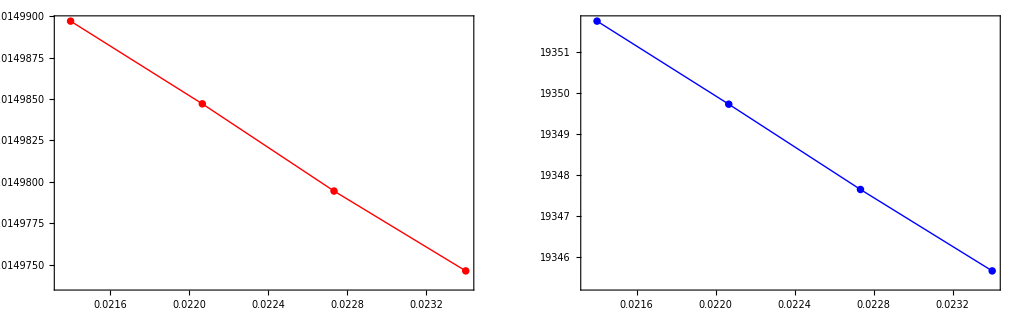

```mathematica
ListPlot[Transpose[{ωbvals,kmaxωb}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\omega_b","k_\\text{max}"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
ListPlot[Transpose[{ωbvals,Pkmaxωb}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Blue]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\omega_b","P(k_\\text{max})"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
GraphicsRow[{%%,%},ImageSize->1020]
```

#### Varying ω_m

```mathematica
(* Load, interpolate and find the {k,P(k)} at the maximum for each Subscript[ω, m] *)MaxPkωm=Table[spectrum=Import[FileNameJoin[{dir,"spectrum_omega_m_"<>ToString[i]<>".txt"}],"Table"];
Pk=Interpolation[spectrum];
FindMaximum[{Pk[k],10^-3<k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6],{i,0,3}];
```

```mathematica
(* Extract values of Subscript[k, eq] and P(Subscript[k, eq]) *)
ωmvals={0.13,0.13666667,0.14333333,0.15}
Pkmaxωm=MaxPkωm[[All,1]]
kmaxωm=MaxPkωm[[All,2,1,2]]
```

{0.13,0.136667,0.143333,0.15}

{19351.8,19269.7,19188.4,19107.9}

{0.0149897,0.0150741,0.0151584,0.0152427}

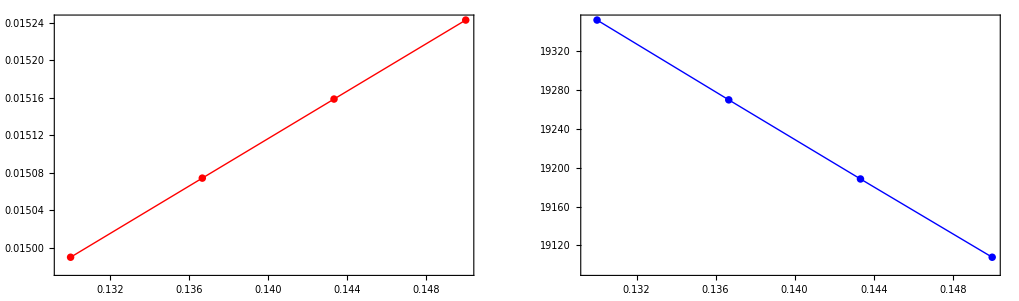

```mathematica
ListPlot[Transpose[{ωmvals,kmaxωm}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\omega_m","k_\\text{max}"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
ListPlot[Transpose[{ωmvals,Pkmaxωm}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Blue]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\omega_m","P(k_\\text{max})"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
GraphicsRow[{%%,%},ImageSize->1020]
```

#### Varying n_s

```mathematica
(* Load, interpolate and find the {k,P(k)} at the maximum for each Subscript[n, s] *)MaxPkns=Table[spectrum=Import[FileNameJoin[{dir,"spectrum_ns_"<>ToString[i]<>".txt"}],"Table"];
Pk=Interpolation[spectrum];
FindMaximum[{Pk[k],10^-3<k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6],{i,0,3}];
```

```mathematica
(* Extract values of Subscript[k, eq] and P(Subscript[k, eq]) *)
nsvals={0.9,0.93333333,0.96666667,1.}
Pkmaxns=MaxPkns[[All,1]]
kmaxns=MaxPkns[[All,2,1,2]]
```

{0.9,0.933333,0.966667,1.}

{19351.8,19220.5,19090.5,18961.7}

{0.0149897,0.0150549,0.01512,0.0151851}

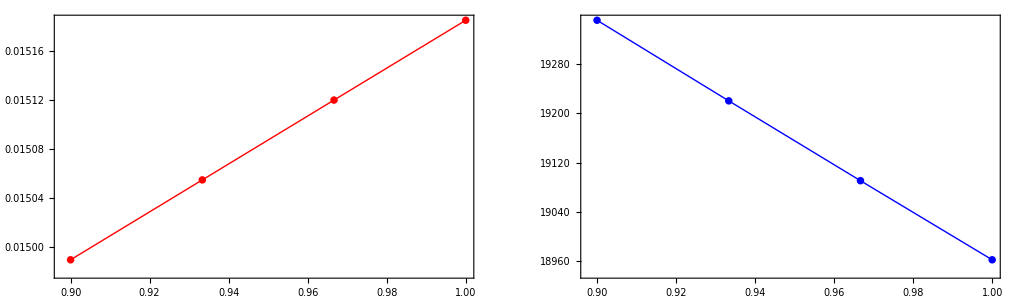

```mathematica
ListPlot[Transpose[{nsvals,kmaxns}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"n_s","k_\\text{max}"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
ListPlot[Transpose[{nsvals,Pkmaxns}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Blue]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"n_s","P(k_\\text{max})"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
GraphicsRow[{%%,%},ImageSize->1020]
```

#### Varying A_s

```mathematica
(* Load, interpolate and find the {k,P(k)} at the maximum for each Subscript[A, s] *)MaxPkAs=Table[spectrum=Import[FileNameJoin[{dir,"spectrum_As_"<>ToString[i]<>".txt"}],"Table"];
Pk=Interpolation[spectrum];
FindMaximum[{Pk[k],10^-3<k<10^-1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6],{i,0,3}];
```

```mathematica
(* Extract values of Subscript[k, eq] and P(Subscript[k, eq]) *)
Asvals={1.5,1.83333333,2.16666667,2.5}
PkmaxAs=MaxPkAs[[All,1]]
kmaxAs=MaxPkAs[[All,2,1,2]]
```

{1.5,1.83333,2.16667,2.5}

{19351.8,19889.3,20426.9,20964.4}

{0.0149897,0.0149897,0.0149897,0.0149897}

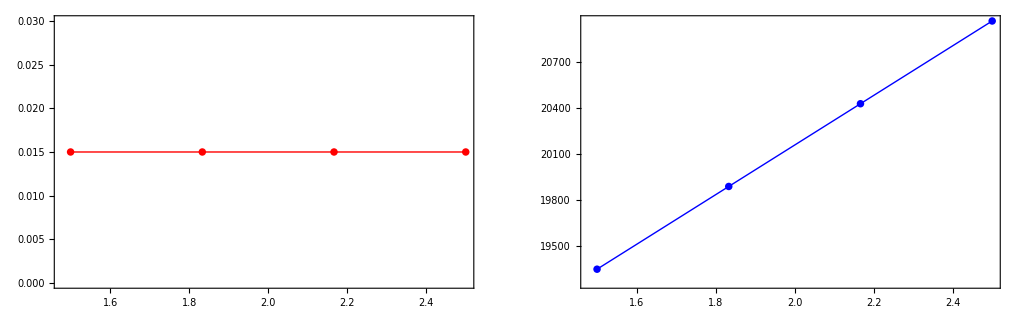

```mathematica
ListPlot[Transpose[{Asvals,kmaxAs}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"A_s","k_\\text{max}"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
ListPlot[Transpose[{Asvals,PkmaxAs}],Joined->True,Mesh->All,PlotStyle->{Directive[Thick,Blue]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"A_s","P(k_\\text{max})"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420];
GraphicsRow[{%%,%},ImageSize->1020]
```

#### Analytical Approximation

```mathematica
(* Function to build arrays varying one parameter at a time *)
varyList[list_,refValue_,paramPos_]:=Table[ReplacePart[{hvals[[1]],ωbvals[[1]],ωmvals[[1]],nsvals[[1]],Asvals[[1]]},paramPos->list[[i]]],{i,1,Length[list]}];
(* Create sublists with the variation of each parameter *)
subdataPkmaxh=MapThread[Append,{varyList[hvals,hvals[[1]],1],Pkmaxh}];
subdataPkmaxωb=MapThread[Append,{varyList[ωbvals,ωbvals[[1]],2],Pkmaxωb}];
subdataPkmaxωm=MapThread[Append,{varyList[ωmvals,ωmvals[[1]],3],Pkmaxωm}];
subdataPkmaxns=MapThread[Append,{varyList[nsvals,nsvals[[1]],4],Pkmaxns}];
subdataPkmaxAs=MapThread[Append,{varyList[Asvals,Asvals[[1]],5],PkmaxAs}];
(* Join everything in one dataset *)
DataSetPkmax=Join[subdataPkmaxh,subdataPkmaxωb,subdataPkmaxωm,subdataPkmaxns,subdataPkmaxAs];
```

```mathematica
(* Ansatz for P(Subscript[k, max]) *)
PkmaxAnalytical[h_,ωb_,ωm_,ns_,As_,Amp_,ak1_,ak2_,ak3_,ak4_]:=Amp*10^4*(h^ak1 ⅇ^(-ak2*ωb))/(ωm^ak3*ns^ak4)*As
```

```mathematica
χPkmax[Amp_,ak1_,ak2_,ak3_,ak4_]:=Mean[Table[Abs[(1-1/DataSetPkmax[[i,6]] PkmaxAnalytical[DataSetPkmax[[i,1]],DataSetPkmax[[i,2]],DataSetPkmax[[i,3]],DataSetPkmax[[i,4]],DataSetPkmax[[i,5]],Amp,ak1,ak2,ak3,ak4])]*100,{i,1,Length[DataSetPkmax]}]]
```

```mathematica
NMinimize[χPkmax[Amp,ak1,ak2,ak3,ak4],{Amp,ak1,ak2,ak3,ak4},Method->"DifferentialEvolution",AccuracyGoal->6,PrecisionGoal->6,MaxIterations->50000]
ParamsPkmax=%[[2]]
```

{0.0307961,{Amp→0.708094,a1→2.08143,a2→1.23033,a3→0.669274,a4→1.49408}}

{Amp→0.708094,a1→2.08143,a2→1.23033,a3→0.669274,a4→1.49408}

```mathematica
i=20;
PkmaxAnalytical[DataSetPkmax[[i,1]],DataSetPkmax[[i,2]],DataSetPkmax[[i,3]],DataSetPkmax[[i,4]],DataSetPkmax[[i,5]],Amp,a1,a2,a3,a4]/.ParamsPkmax
DataSetPkmax[[i,6]]
i=.;
```

32252.9

32252.9

```mathematica
(* Function to build arrays varying one parameter at a time *)
varyList[list_,refValue_,paramPos_]:=Table[ReplacePart[{hvals[[1]],ωbvals[[1]],ωmvals[[1]],nsvals[[1]]},paramPos->list[[i]]],{i,1,Length[list]}];
(* Create sublists with the variation of each parameter *)
subdatakmaxh=MapThread[Append,{varyList[hvals,hvals[[1]],1],kmaxh}];
subdatakmaxωb=MapThread[Append,{varyList[ωbvals,ωbvals[[1]],2],kmaxωb}];
subdatakmaxωm=MapThread[Append,{varyList[ωmvals,ωmvals[[1]],3],kmaxωm}];
subdatakmaxns=MapThread[Append,{varyList[nsvals,nsvals[[1]],4],kmaxns}];
(* Join everything in one dataset *)
DataSetkmax=Join[subdatakmaxh,subdatakmaxωb,subdatakmaxωm,subdatakmaxns];
```

```mathematica
(* Ansatz for Subscript[k, max] *)
kmaxAnalytical[h_,ωb_,ωm_,ns_,A_,ak1_,ak2_,ak3_,ak4_,ak5_]:=A*(ωm^ak1*ns^ak2)/(h^ak3*(1+ak4*ωb)^ak5)
```

```mathematica
χkmax[A_,ak1_,ak2_,ak3_,ak4_,ak5_]:=Mean[Table[Abs[1-1/DataSetkmax[[i,5]](kmaxAnalytical[DataSetkmax[[i,1]],DataSetkmax[[i,2]],DataSetkmax[[i,3]],DataSetkmax[[i,4]],A,ak1,ak2,ak3,ak4,ak5])]*100,{i,Length[DataSetkmax]}]]
```

```mathematica
NMinimize[χkmax[A,a1,a2,a3,a4,a5],{A,a1,a2,a3,a4,a5},Method->"DifferentialEvolution",AccuracyGoal->6,PrecisionGoal->6,MaxIterations->10000]
Paramskmax=%[[2]]
```

{0.011852,{A→0.0706619,a1→0.882421,a2→0.939057,a3→1.00649,a4→1.20249,a5→3.33952}}

{A→0.0706619,a1→0.882421,a2→0.939057,a3→1.00649,a4→1.20249,a5→3.33952}

```mathematica
i=5;
kmaxAnalytical[DataSetkmax[[i,1]],DataSetkmax[[i,2]],DataSetkmax[[i,3]],DataSetkmax[[i,4]],A,ak1,ak2,ak3,ak4,ak5]/.Paramskmax
DataSetkmax[[i,5]]
i=.;
```

0.0149897

0.0149897

```mathematica
PkmaxAnalytical[h,ωb,ωm,ns,As,Amp,ak1,ak2,ak3,ak4]/.ParamsPkmax
kmaxAnalytical[h,ωb,ωm,ns,A,ak1,ak2,ak3,ak4,ak5]/.Paramskmax
```

(7080.94 As ⅇ^(-1.23033 ωb) h^2.08143)/(ns^1.49408 ωm^0.669274)

(0.0706619 ns^0.939057 ωm^0.882421)/(h^1.00649 (1+1.20249 ωb)^3.33952)

#### Test

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
paths=FileNameJoin[{"./Data/spectra_latin_hc/spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

```mathematica
Pclass=ParallelTable[Interpolation[PkData[[i]]],{i,1,Length[PkData]}];
```

```mathematica
Pkmaxclass=ParallelTable[FindMaximum[{Pclass[[i]][k],k>10^-3&&k<1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[1]],{i,1,Length[Pclass]}];
```

```mathematica
kmaxclass=ParallelTable[FindMaximum[{Pclass[[i]][k],k>10^-3&&k<1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[2,1,2]],{i,1,Length[Pclass]}];
```

```mathematica
Pkmax[h_,ωb_,ωm_,ns_,As_]:=(7080.944As ⅇ^(-1.230ωb) h^("2.081"))/(ns^1.5 ωm^("0.669"))
kmax[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
```

```mathematica
TestPkmax=Table[Abs[1-Pkmax[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]]]/Pkmaxclass[[i]]]*100,{i,1,Length[PkData]}];
{Mean[#],Median[#],Min[#],Max[#]}&@TestPkmax
```

{0.268346,0.190368,0.000713166,1.02244}

```mathematica
Testkmax=Table[Abs[1-kmax[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]]]/kmaxclass[[i]]]*100,{i,1,Length[PkData]}];
{Mean[#],Median[#],Min[#],Max[#]}&@Testkmax
```

{0.0405622,0.0305059,0.00004654,0.173617}

### R(k_eq) = P_Class(k_eq)/P_GA(k_eq)

#### Fitting Function

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]
PGA[k_,h_,ωb_,ωm_,ns_,A_]:=A*k^ns*TGA[k,h,ωb,ωm]^2
kmax[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
```

#### Parameters

```mathematica
dir="./Data/Spectra_kmax";
```

```mathematica
hvals={0.65,0.683,0.716,0.75};
ωbvals={0.0214,0.02206667,0.02273333,0.0234};
ωmvals={0.13,0.13666667,0.14333333,0.15};
nsvals={0.9,0.93333333,0.96666667,1.};
Asvals={1.5,1.83333333,2.16666667,2.5};
href=hvals[[1]];
ωbref=ωbvals[[1]];
ωmref=ωmvals[[1]];
nsref=nsvals[[1]];
Asref=Asvals[[1]];
```

#### Varying h

```mathematica
(* Define spectra and params *)
spectrah=Table[Import[dir<>"/spectrum_h_"<>ToString[i]<>".txt","Table"],{i,0,3}];
(* Function for error minimization *)
getAh[spectrum_,h_]:=Module[{res},res=FindMinimum[Mean[Table[100*Abs[1-PGA[spectrum[[i,1]],h,ωbref,ωmref,nsref,A0]/spectrum[[i,2]]],{i,Length[spectrum]}]],{A0,10^6,10^7}];
A0/. Last[res]]
(* Apply to all spectra *)
Ah=Table[getAh[spectrah[[i]],hvals[[i]]],{i,1,4}]
```

{1.92371×10^6,2.00664×10^6,2.07467×10^6,2.13328×10^6}

```mathematica
Pkmaxh={19351.765017011498,19610.073184287678,19870.056964181294,20131.40609461821};
```

```mathematica
Rmaxh=Table[Pkmaxh[[i]]/PGA[kmaxh[[i]],hvals[[i]],ωbref,ωmref,nsref,Ah[[i]]],{i,1,4}]
```

{1.00738,1.02549,1.05266,1.08742}

#### Varying ω_b

```mathematica
(* Define spectra and params *)
spectraωb=Table[Import[dir<>"/spectrum_omega_b_"<>ToString[i]<>".txt","Table"],{i,0,3}];
(* Function for error minimization *)
getAωb[spectrum_,ωb_]:=Module[{res},res=FindMinimum[Mean[Table[100*Abs[1-PGA[spectrum[[i,1]],href,ωb,ωmref,nsref,A0]/spectrum[[i,2]]],{i,Length[spectrum]}]],{A0,10^6,10^7}];
A0/. Last[res]]
(* Apply to all spectra *)
Aωb=Table[getAωb[spectraωb[[i]],ωbvals[[i]]],{i,1,4}]
```

{1.92371×10^6,1.93579×10^6,1.94138×10^6,1.94963×10^6}

```mathematica
Pkmaxωb={19351.765017011498,19349.732524893425,19347.64581792242,19345.653783137164};
```

```mathematica
Rmaxωb=Table[Pkmaxωb[[i]]/PGA[kmaxωb[[i]],href,ωbvals[[i]],ωmref,nsref,Aωb[[i]]],{i,1,4}]
```

{1.00738,1.00672,1.00951,1.01102}

#### Varying ω_m

```mathematica
(* Define spectra and params *)
spectraωm=Table[Import[dir<>"/spectrum_omega_m_"<>ToString[i]<>".txt","Table"],{i,0,3}];
(* Function for error minimization *)
getAωm[spectrum_,ωm_]:=Module[{res},res=FindMinimum[Mean[Table[100*Abs[1-PGA[spectrum[[i,1]],href,ωbref,ωm,nsref,A0]/spectrum[[i,2]]],{i,Length[spectrum]}]],{A0,10^6,10^7}];
A0/. Last[res]]
(* Apply to all spectra *)
Aωm=Table[getAωm[spectraωm[[i]],ωmvals[[i]]],{i,1,4}]
```

{1.92371×10^6,1.82616×10^6,1.69172×10^6,1.5229×10^6}

```mathematica
Pkmaxωm={19351.765017011498,19269.723281303544,19188.38522039866,19107.934950461};
```

```mathematica
Rmaxωm=Table[Pkmaxωm[[i]]/PGA[kmaxωm[[i]],href,ωbref,ωmvals[[i]],nsref,Aωm[[i]]],{i,1,4}]
```

{1.00738,1.00179,1.02639,1.08714}

#### Varying n_s

```mathematica
(* Define spectra and params *)
spectrans=Table[Import[dir<>"/spectrum_ns_"<>ToString[i]<>".txt","Table"],{i,0,3}];
(* Function for error minimization *)
getAns[spectrum_,ns_]:=Module[{res},res=FindMinimum[Mean[Table[100*Abs[1-PGA[spectrum[[i,1]],href,ωbref,ωmref,ns,A0]/spectrum[[i,2]]],{i,Length[spectrum]}]],{A0,10^6,10^7}];
A0/. Last[res]]
(* Apply to all spectra *)
Ans=Table[getAns[spectrans[[i]],nsvals[[i]]],{i,1,4}]
```

{1.92371×10^6,2.21474×10^6,2.49349×10^6,2.73531×10^6}

```mathematica
Pkmaxns={19351.765017011498,19220.517366964843,19090.504018073407,18961.7104456484};
```

```mathematica
Rmaxns=Table[Pkmaxns[[i]]/PGA[kmaxns[[i]],href,ωbref,ωmref,nsvals[[i]],Ans[[i]]],{i,1,4}]
```

{1.00738,0.999676,1.01417,1.05571}

#### Varying A_s

```mathematica
(* Define spectra and params *)
spectraAs=Table[Import[dir<>"/spectrum_As_"<>ToString[i]<>".txt","Table"],{i,0,3}];
(* Function for error minimization *)
getAAs[spectrum_,As_]:=Module[{res},res=FindMinimum[Mean[Table[100*Abs[1-PGA[spectrum[[i,1]],href,ωbref,ωmref,nsref,A0]/spectrum[[i,2]]],{i,Length[spectrum]}]],{A0,10^6,10^7}];
A0/. Last[res]]
(* Apply to all spectra *)
AAs=Table[getAAs[spectraAs[[i]],Asvals[[i]]],{i,1,4}]
```

{1.92371×10^6,1.97715×10^6,2.03058×10^6,2.08402×10^6}

```mathematica
PkmaxAs={19351.765017011498,19889.314043819577,20426.86310269053,20964.41212328742};
```

```mathematica
RmaxAs=Table[PkmaxAs[[i]]/PGA[kmax[href,ωbref,ωmref,nsref],href,ωbref,ωmref,nsref,AAs[[i]]],{i,1,4}]
```

{1.00738,1.00738,1.00738,1.00738}

#### Analytical Approximation

```mathematica
Rmaxh
Rmaxωb
Rmaxωm
Rmaxns
RmaxAs
```

{1.00738,1.02549,1.05266,1.08742}

{1.00738,1.00672,1.00951,1.01102}

{1.00738,1.00179,1.02639,1.08714}

{1.00738,0.999676,1.01417,1.05571}

{1.00738,1.00738,1.00738,1.00738}

```mathematica
(* Function to build arrays varying one parameter at a time *)
varyList[list_,refValue_,paramPos_]:=Table[ReplacePart[{hvals[[1]],ωbvals[[1]],ωmvals[[1]],nsvals[[1]]},paramPos->list[[i]]],{i,1,Length[list]}];
(* Create sublists with the variation of each parameter *)
subdataRmaxh=MapThread[Append,{varyList[hvals,hvals[[1]],1],Rmaxh}];
subdataRmaxωb=MapThread[Append,{varyList[ωbvals,ωbvals[[1]],2],Rmaxωb}];
subdataRmaxωm=MapThread[Append,{varyList[ωmvals,ωmvals[[1]],3],Rmaxωm}];
subdataRmaxns=MapThread[Append,{varyList[nsvals,nsvals[[1]],4],Rmaxns}];
(* Join everything in one dataset *)
DataSetRmax=Join[subdataRmaxh,subdataRmaxωb,subdataRmaxωm,subdataRmaxns];
```

```mathematica
RmaxAnalytical[h_,ωb_,ωm_,ns_,ak1_,ak2_,ak3_,ak4_,ak5_]:=ak1+ak2*h^2+ak3*ωb+ak4/ωm+ak5*ns
```

```mathematica
χkmax[ak1_,ak2_,ak3_,ak4_,ak5_]:=Mean[Table[Abs[1-(RmaxAnalytical[DataSetRmax[[i,1]],DataSetRmax[[i,2]],DataSetRmax[[i,3]],DataSetRmax[[i,4]],ak1,ak2,ak3,ak4,ak5]/DataSetRmax[[i,5]])]*100,{i,Length[DataSetRmax]}]]
```

```mathematica
NMinimize[χkmax[ak1,ak2,ak3,ak4,ak5],{ak1,ak2,ak3,ak4,ak5},Method->"DifferentialEvolution",AccuracyGoal->6,PrecisionGoal->6,MaxIterations->10000]
ParamsRmax=%[[2]]
```

{0.00842741,{a1→0.646093,a2→-0.00970801,a3→7.17281,a4→0.0239205,a5→0.0307467}}

{a1→0.646093,a2→-0.00970801,a3→7.17281,a4→0.0239205,a5→0.0307467}

```mathematica
Rmax[h_,ωb_,ωm_,ns_]:=ak1+ak2*h^2+ak3*ωb+ak4/ωm+ak5*ns/.ParamsRmax
NumberForm[Req[h,ωb,ωm,ns],{Infinity,4}]
```

0.6461-0.0097 h^2+0.0307 ns+7.1728 ωb+0.0239/ωm

```mathematica
i=3;
Rmax[DataSetRmax[[i,1]],DataSetRmax[[i,2]],DataSetRmax[[i,3]],DataSetRmax[[i,4]]]
DataSetRmax[[i,5]]
i=.;
```

1.00629

1.00658

#### Test

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
paths=FileNameJoin[{"./Data/spectra_latin_hc/spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

```mathematica
Pclass=ParallelTable[Interpolation[PkData[[i]]],{i,1,Length[PkData]}];
```

```mathematica
Pkmaxclass=ParallelTable[FindMaximum[{Pclass[[i]][k],k>10^-3&&k<1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[1]],{i,1,Length[Pclass]}];
kmaxclass=ParallelTable[FindMaximum[{Pclass[[i]][k],k>10^-3&&k<1},{k,0.01},AccuracyGoal->6,PrecisionGoal->6][[2,1,2]],{i,1,Length[Pclass]}];
```

```mathematica
MAPEGA[A_,i_]:=Mean[Table[100*Abs[1-PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A]/(PkData[[i]][[j,2]])],{j,Length[PkData[[i]]]}]];
FindAGA=ParallelTable[FindMinimum[MAPEGA[A,i],{A,10^6,10^7}],{i,Length[PkData]}]//Quiet;
AGA=FindAGA[[All,2,1,2]]//Quiet;
{Mean[#],Min[#],Max[#]}&@FindAGA[[All,1]]//Quiet
(* At this point, the formula is 0.33% accurate on average *)
```

{0.333207,0.183223,0.631655}

```mathematica
RmaxNum[i_]:=Pkmaxclass[[i]]/PGA[kmaxclass[[i]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],AGA[[i]]]
Rmax[h_,ωb_,ωm_,ns_]:="0.6461"-"0.0097" h^("2")+"0.0307" ns+"7.1728" ωb+("0.0239")/ωm
```

```mathematica
TestRmax=Table[Abs[1-Rmax[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]]]/RmaxNum[i]]*100,{i,1,Length[PkData]}];
{Mean[#],Min[#],Max[#]}&@TestRmax
```

{0.0851422,0.000436246,0.362228}

### P_GA(k_eq), P_GA'(k_eq)

#### Fitting Function

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]
PGA[k_,h_,ωb_,ωm_,ns_,A_]:=A*k^ns*TGA[k,h,ωb,ωm]^2
DPGA[k_,h_,ωb_,ωm_,ns_,A_]=D[PGA[k,h,ωb,ωm,ns,A],k];
Dmaxnw[h_,ωb_,ωm_,ns_]:=(ns/k+2D[Log[TGA[k,h,ωb,ωm]],k])/.k->kmax[h,ωb,ωm,ns]
kmax[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
```

#### Varying Parameters

```mathematica
hvals={0.65,0.683,0.716,0.75};
ωbvals={0.0214,0.02206667,0.02273333,0.0234};
ωmvals={0.13,0.13666667,0.14333333,0.15};
nsvals={0.9,0.93333333,0.96666667,1.};
Asvals={1.5,1.83333333,2.16666667,2.5};
href=hvals[[1]];
ωbref=ωbvals[[1]];
ωmref=ωmvals[[1]];
nsref=nsvals[[1]];
Asref=Asvals[[1]];
```

```mathematica
PGAkmaxh=Table[PGA[kmax[hvals[[i]],ωbref,ωmref,nsref],hvals[[i]],ωbref,ωmref,nsref,A]/A,{i,1,4}]
PGAkmaxωb=Table[PGA[kmax[href,ωbvals[[i]],ωmref,nsref],href,ωbvals[[i]],ωmref,nsref,A]/A,{i,1,4}]
PGAkmaxωm=Table[PGA[kmax[href,ωbref,ωmvals[[i]],nsref],href,ωbref,ωmvals[[i]],nsref,A]/A,{i,1,4}]
PGAkmaxns=Table[PGA[kmax[href,ωbref,ωmref,nsvals[[i]]],href,ωbref,ωmref,nsvals[[i]],A]/A,{i,1,4}]
```

{0.00998587,0.00955066,0.00915365,0.00877939}

{0.00998587,0.00992987,0.00987373,0.00981744}

{0.00998587,0.0105342,0.0110772,0.0116151}

{0.00998587,0.00867733,0.0075487,0.00657401}

```mathematica
DPGAkmaxh=Table[DPGA[kmax[hvals[[i]],ωbref,ωmref,nsref],hvals[[i]],ωbref,ωmref,nsref,A]/A,{i,1,4}]
DPGAkmaxωb=Table[DPGA[kmax[href,ωbvals[[i]],ωmref,nsref],href,ωbvals[[i]],ωmref,nsref,A]/A,{i,1,4}]
DPGAkmaxωm=Table[DPGA[kmax[href,ωbref,ωmvals[[i]],nsref],href,ωbref,ωmvals[[i]],nsref,A]/A,{i,1,4}]
DPGAkmaxns=Table[DPGA[kmax[href,ωbref,ωmref,nsvals[[i]]],href,ωbref,ωmref,nsvals[[i]],A]/A,{i,1,4}]
```

{-0.0194653,-0.0193542,-0.019247,-0.01914}

{-0.0194653,-0.0214844,-0.0235207,-0.0255738}

{-0.0194653,-0.010865,-0.00289718,0.00451348}

{-0.0194653,-0.0169856,-0.0147416,-0.0127221}

#### Analytical Approximation

```mathematica
(* Function to build arrays varying one parameter at a time *)
varyList[list_,refValue_,paramPos_]:=Table[ReplacePart[{hvals[[1]],ωbvals[[1]],ωmvals[[1]],nsvals[[1]]},paramPos->list[[i]]],{i,1,Length[list]}];
(* Create sublists with the variation of each parameter *)
subdataPGAkmaxh=MapThread[Append,{varyList[hvals,hvals[[1]],1],PGAkmaxh}];
subdataPGAkmaxωb=MapThread[Append,{varyList[ωbvals,ωbvals[[1]],2],PGAkmaxωb}];
subdataPGAkmaxωm=MapThread[Append,{varyList[ωmvals,ωmvals[[1]],3],PGAkmaxωm}];
subdataPGAkmaxns=MapThread[Append,{varyList[nsvals,nsvals[[1]],4],PGAkmaxns}];
(* Join everything in one dataset *)
DataSetPGAkmax=Join[subdataPGAkmaxh,subdataPGAkmaxωb,subdataPGAkmaxωm,subdataPGAkmaxns];
```

```mathematica
PGAkmax[h_,ωb_,ωm_,ns_,Amp_,ak1_,ak2_,ak3_,ak4_]:=Amp*(h^ak1 ⅇ^(-ak2*ωb))/(ωm^ak3*ns^ak4)
```

```mathematica
χPGAkmax[Amp_,ak1_,ak2_,ak3_,ak4_]:=Mean[Table[Abs[(1-1/DataSetPGAkmax[[i,5]] PGAkmax[DataSetPGAkmax[[i,1]],DataSetPGAkmax[[i,2]],DataSetPGAkmax[[i,3]],DataSetPGAkmax[[i,4]],Amp,ak1,ak2,ak3,ak4])]*100,{i,1,Length[DataSetPGAkmax]}]]
```

```mathematica
NMinimize[χPGAkmax[Amp,ak1,ak2,ak3,ak4],{Amp,ak1,ak2,ak3,ak4},Method->"DifferentialEvolution",AccuracyGoal->6,PrecisionGoal->6,MaxIterations->10000]
ParamsPGAkmax=%[[2]]
```

{0.0547884,{Amp→0.0470036,ak1→-0.89981,ak2→8.50468,ak3→-1.06224,ak4→3.91547}}

{Amp→0.0470036,ak1→-0.89981,ak2→8.50468,ak3→-1.06224,ak4→3.91547}

```mathematica
i=3;
PGAkmax[DataSetPGAkmax[[i,1]],DataSetPGAkmax[[i,2]],DataSetPGAkmax[[i,3]],DataSetPGAkmax[[i,4]],Amp,ak1,ak2,ak3,ak4]/.ParamsPGAkmax
DataSetPGAkmax[[i,5]]
i=.;
```

0.00915365

0.00915365

```mathematica
(* Create sublists with the variation of each parameter *)
subdataDPGAkmaxh=MapThread[Append,{varyList[hvals,hvals[[1]],1],DPGAkmaxh}];
subdataDPGAkmaxωb=MapThread[Append,{varyList[ωbvals,ωbvals[[1]],2],DPGAkmaxωb}];
subdataDPGAkmaxωm=MapThread[Append,{varyList[ωmvals,ωmvals[[1]],3],DPGAkmaxωm}];
subdataDPGAkmaxns=MapThread[Append,{varyList[nsvals,nsvals[[1]],4],DPGAkmaxns}];
(* Join everything in one dataset *)
DataSetDPGAkmax=Join[subdataDPGAkmaxh,subdataDPGAkmaxωb,subdataDPGAkmaxωm,subdataDPGAkmaxns];
```

```mathematica
X=DataSetDPGAkmax[[All,;;4]];   (*Input parameters*)
Y=DataSetDPGAkmax[[All,-1]];     (*True values*)
lm=LinearModelFit[DataSetDPGAkmax,{1,h,h^2,ωb, ωb^2,ωm,ωm^2,ns,ns^2},{h,ωb,ωm,ns}];
%["RSquared"]
DPGAkmax[h_,ωb_,ωm_,ns_]=%%["BestFit"]
```

1.

-0.406487+0.00518256 h-0.00138618 h^2+0.26388 ns-0.103402 ns^2-2.22731 ωb-18.4713 ωb^2+3.07681 ωm-6.70757 ωm^2

```mathematica
DataSetDPGAkmax[[All,;;4]]//Length
```

16

```mathematica
MSE=Mean[Table[(DPGAkmax@@X[[i]]-Y[[i]])^2,{i,1,Length[X]}]]
MAE=Mean[Table[Abs[DPGAkmax@@X[[i]]-Y[[i]]],{i,1,Length[X]}]]
MPE=Mean[Table[100*Abs[1-(DPGAkmax@@X[[i]])/Y[[i]]],{i,Length[X]}]]
```

1.87795×10^-11

2.24706×10^-6

0.0405343

```mathematica
i=6;
DPGAkmax@@X[[i]]
DataSetDPGAkmax[[i,5]]
i=.;
```

-0.0214843

-0.0214844

```mathematica
PGAkmax[h,ωb,ωm,ns,Amp,ak1,ak2,ak3,ak4]/.ParamsPGAkmax
DPGAkmax[h,ωb,ωm,ns]
```

(0.0470036 ⅇ^(-8.50468 ωb) ωm^1.06224)/(h^0.89981 ns^3.91547)

-0.406487+0.00518256 h-0.00138618 h^2+0.26388 ns-0.103402 ns^2-2.22731 ωb-18.4713 ωb^2+3.07681 ωm-6.70757 ωm^2

## Correction

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[];
Off[General::munfl];
Off[General::stop];
Off[Infinity::indet];
Off[Power::infy];
Off[Indeterminate::indet];
```

### Data

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
dir="./Data/spectra_latin_hc/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

### Fitting Function

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
AS2=0.00837;
kS2=0.081;
σS2=0.0404;
AS3=0.012538;
kS3=0.14376;
σS3=0.007586;
AS4=0.0038985;
kS4=1.1791;
σS4=0.3;

q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)

fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]

PS2[k_]:=1+AS2*ⅇ^(-((k-kS2)/σS2)^2)
PS3[k_]:=1-AS3*ⅇ^(-((k-kS3)/σS3)^2)
PS4[k_]:=1-AS4*ⅇ^(-((k-kS4)/σS4)^2)

PGA[k_,h_,ωb_,ωm_,ns_,A0_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2*PS2[k]*PS3[k]*PS4[k]

kmax[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
Pkmax[h_,ωb_,ωm_,ns_,As_]:=(7080.944 As ⅇ^(-1.2303 ωb) h^2.081426)/(ns^1.49408 ωm^0.66927)
Rmax[h_,ωb_,ωm_,ns_]:=0.6461-0.0097 h^2+0.0307ns+7.1728ωb+0.0239/ωm
PGAmax[h_,ωb_,ωm_,ns_]:=(0.04682 ⅇ^(-8.611 ωb) ωm^1.0587)/(h^0.8998 ns^3.916)
DPGAmax[h_,ωb_,ωm_,ns_]:=-0.38598+0.005318h-0.00145 h^2+0.2277ns-0.086155 ns^2-1.86 ωb-28.6088 ωb^2+2.9997ωm-6.426 ωm^2
Bmax[h_,ωb_,ωm_,ns_]:=Rmax[h,ωb,ωm,ns]-1
Amax[h_,ωb_,ωm_,ns_,σmax_,λmax_]:=-(DPGAmax[h,ωb,ωm,ns]/PGAmax[h,ωb,ωm,ns])(1+Bmax[h,ωb,ωm,ns])-√(2/π)(λmax/σmax)Bmax[h,ωb,ωm,ns]
Pmax[k_,h_,ωb_,ωm_,ns_,σmax_,λmax_]:=1+(Amax[h,ωb,ωm,ns,σmax,λmax](k-kmax[h,ωb,ωm,ns])+Bmax[h,ωb,ωm,ns])ⅇ^(-1/2(k-kmax[h,ωb,ωm,ns])^2/σmax^2)(1+Erf[λmax*(k-kmax[h,ωb,ωm,ns])/(√2 σmax)])
```

### Compute Normalization

```mathematica
R8=8;            (* Mpc h^-1 *)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]); (* Top-hat Filter *)
σ8=Params[[All,6]];
IntegralGA[i_]:=NIntegrate[k^(Params[[i,4]]+2) Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GA=ParallelTable[2*π^2 σ8[[i]]^2/IntegralGA[i],{i,1,Length[Params]}];
```

```mathematica
MAPEGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]/(PkData[[i]][[j,2]])]},{j,Length[PkData[[i]]]}];
```

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet
```

{0.382257,0.137184,0.640745,{{177}},{{86}}}

### Full Correction

```mathematica
MeanAccGA[A_,i_]:=Mean[Table[100*Abs[1-PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A]/(PkData[[i]][[j,2]])],{j,Length[PkData[[i]]]}]];
FindAGA=Table[FindMinimum[MeanAccGA[A,i],{A,10^6,10^7},AccuracyGoal->6,PrecisionGoal->6],{i,Length[PkData]}]//Quiet;
AGA=FindAGA[[All,2,1,2]];
```

```mathematica
(* Accuracy of Subscript[A, 0] computation from estimation *)
Table[Abs[1-A0GA[[i]]/AGA[[i]]]*100,{i,Length[A0GA]}];
{Mean[#],Median[#],Max[#],Min[#],Quantile[#,0.68],Quantile[#,0.95]}&@%
```

{0.227333,0.207126,0.632262,0.00159714,0.298894,0.482626}

```mathematica
FindAGA[[All,1]]//Mean
```

0.334095

```mathematica
χ2Pk[i_][σ_,λ_]:=Mean[Table[Abs[1-(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],AGA[[i]]]*Pc[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σ,λ])/PkData[[i]][[j,2]]]*100,{j,1,Length[PkData[[i]]]}]]
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][σ,λ],{σ,λ},Method->"DifferentialEvolution",MaxIterations->500]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPGA=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 23.0455

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@FindAGA[[All,1]]
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@ParamsPGA[[All,1]]
```

{0.334095,0.144514,0.636749,{{163}},{{25}}}

{0.200686,0.110604,0.340792,{{3}},{{18}}}

```mathematica
σGA=ParamsPGA[[All,2]][[All,1,2]];
λGA=ParamsPGA[[All,2]][[All,2,2]];
```

```mathematica
AccGAλσ[i_]:=Table[{PkData[[i]][[j,1]],Abs[1-(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],AGA[[i]]]*Pc[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σGA[[i]],λGA[[i]]])/PkData[[i]][[j,2]]]*100},{j,1,Length[PkData[[i]]]}]
```

```mathematica
BestFit=Position[ParamsPGA[[All,1]],Min[ParamsPGA[[All,1]]]][[1,1]];
WorstFit=Position[ParamsPGA[[All,1]],Max[ParamsPGA[[All,1]]]][[1,1]];
```

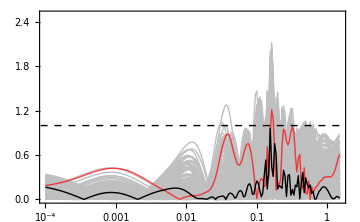

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[AccGAλσ[i],{i,Select[Range[Length[Params]],#!=BestFit&&#!=WorstFit&]}],{AccGAλσ[WorstFit],AccGAλσ[BestFit]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Test set}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},{0,2.5}},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,14},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->Medium]//Quiet]//Quiet
```

```mathematica
(* Calcular diferencias relativas *)
RelDiffGA=Table[1-1/(PkData[[i]][[j,2]])*PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pc[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σGA[[i]],λGA[[i]]],{i,Length[PkData]},{j,Length[PkData[[i]]]}]//Quiet;
(* Extraer valores de k *)
ks=PkData[[1]][[All,1]];
(* Calcular percentiles por punto en k *)
percentiles=Quantile[Transpose[RelDiffGA],{0.5-0.34-0.136,0.5-0.34,0.5,0.5+0.34,0.5+0.34+0.136}];
{low2σ,low1σ,median,up1σ,up2σ}=Transpose[percentiles];
Show[ListLinePlot[{Transpose[{ks,low2σ}],Transpose[{ks,up2σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.890,0.102,0.110],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"}],ListLinePlot[{Transpose[{ks,low1σ}],Transpose[{ks,up1σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.121,0.466,0.705],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"}],ListLinePlot[Transpose[{ks,median}],PlotStyle->Directive[Black,Thick],PlotLegends->None,ScalingFunctions->{"Log","Linear"}],ListLinePlot[{{{Min[ks],0},{Max[ks],0}},{{Min[ks],0.01},{Max[ks],0.01}},{{Min[ks],-0.01},{Max[ks],-0.01}}},PlotStyle->{Directive[Dashed,Black]},Joined->True,ScalingFunctions->{"Log","Linear"}],(*Etiquetas con barras de color*)Epilog->{Inset[Framed[Column[{Row[{Graphics[{RGBColor[0.890,0.102,0.110],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["2\\sigma",Magnification->1.2]}],Row[{Graphics[{RGBColor[0.121,0.466,0.705],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["1\\sigma",Magnification->1.2]}]},Spacings->0.1],RoundingRadius->5,Background->White,FrameStyle->Black,FrameMargins->Small],Scaled[{0.085,0.115}]]},
PlotLabel->MaTeX["\\text{This~work}",Magnification->1.4],
Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k~[h/\\mathrm{Mpc}]",Magnification->1.4],MaTeX["\\Delta P_\\mathrm{lin}/P_\\mathrm{lin, True}",Magnification->1.4]},PlotRange->{{0.01,1.4}//Log,{-0.015,0.015}},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->Large,AspectRatio->0.5]
```

-Graphics-

### Correction: Full Emulator

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λmax=0.4;
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, eq] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
(* Fix λ = 0.4 *)
DDP=Table[D[D[PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pmax[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σmax,λmax],k],k]/.k->kmax[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]]],{i,1,Length[Params]}]//Simplify;
σDDP=Table[Solve[DDP[[i]]==DDPkclass[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]]],σmax]//Quiet,{i,Length[Params]}];
(* Take the smallest one in absolute value *)
MinAbsKeepSign[pair_]:=First@MinimalBy[pair,Abs]
σmaxGA=MinAbsKeepSign/@Table[{Re[σDDP[[i]][[1,1,2]]],Re[σDDP[[i]][[2,1,2]]]},{i,1,Length[Params]}];
```

```mathematica
MAPEσGA[i_]:=Table[{PkData[[i]][[j,1]],Abs[1-(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pmax[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σmaxGA[[i]],λmax])/PkData[[i]][[j,2]]]*100},{j,1,Length[PkData[[i]]]}]
```

```mathematica
Table[Mean[MAPEσGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet;
{Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@%
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@%%
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[MAPEσGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet;
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[MAPEσGA[i][[All,2]]],{i,1,Length[Params]}]//Quiet;
```

{0.128428,0.690662,{{69}},{{83}}}

{0.302715,0.287172,0.339952,0.487617}

```mathematica
MAPEGAσ[i_][σ_]:=Table[{PkData[[i]][[j,1]],Abs[1-(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pmax[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σ,λmax])/PkData[[i]][[j,2]]]*100},{j,1,Length[PkData[[i]]]}]
```

Blue: Original

Black: -Graphics- = -0.0341103

Red: -Graphics- = 0.00783969

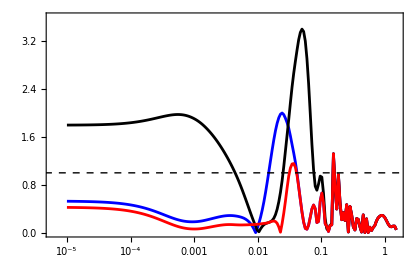

```mathematica
i=4;
Print["Blue: Original"]
Print["Black: ",(MaTeX["\\sigma",Magnification->1.2])," = ",σDDP[[i]][[1,1,2]]]
Print["Red: ",(MaTeX["\\sigma",Magnification->1.2])," = ",σDDP[[i]][[2,1,2]]]
ListLogLinearPlot[{MAPEGA[i],MAPEGAσ[i][Re[σDDP[[i]][[1,1,2]]]],MAPEGAσ[i][σDDP[[i]][[2,1,2]]]},Joined->True,PlotRange->{All,{Automatic,3.6}},PlotStyle->{Directive[Blue],Directive[Black],Directive[Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->420]//Quiet
i=.;
```

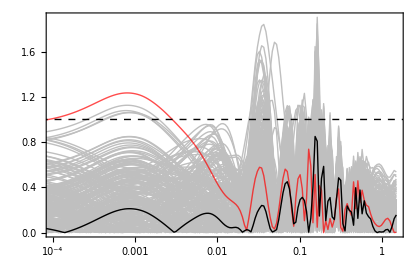

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[MAPEσGA[i],{i,Select[Range[Length[Params]],#!=BestFit&&#!=WorstFit&]}],{MAPEσGA[WorstFit],MAPEσGA[BestFit]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Test set}"],(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},All},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k~[h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->420]//Quiet]//Quiet
```

```mathematica
Comparisonσ=Table[{MAPEσGA[i][[All,2]]//Mean,MAPEGA[i][[All,2]]//Mean},{i,Length[Params]}];
Posσ=Position[Comparisonσ,{a_,b_}/;b<a]//Flatten
Length[Posσ]
```

{2,7,12,15,18,19,21,23,59,61,75,82,83,95,102,109,110,118,120,126,128,131,133,137,139,144,149,158,163,175,177,179,186,188,196}

35

```mathematica
ValidIndices=Complement[Range[Length[PkData]],Posσ];MAPEσLast=Table[Table[{PkData[[i]][[j,1]],Abs[1-(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pmax[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σmaxGA[[i]],λmax])/PkData[[i]][[j,2]]]*100},{j,1,Length[PkData[[i]]]}],{i,ValidIndices}];
```

```mathematica
Table[Mean[MAPEσLast[[i]][[All,2]]],{i,1,Length[ValidIndices]}]//Quiet;
{Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@%
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@%%
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[MAPEσLast[[i]][[All,2]]],{i,1,Length[ValidIndices]}]//Quiet;
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[MAPEσLast[[i]][[All,2]]],{i,1,Length[ValidIndices]}]//Quiet;
```

{0.128428,0.571328,{{59}},{{124}}}

{0.282302,0.274014,0.307207,0.445803}

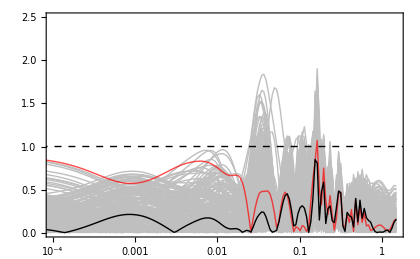

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[MAPEσLast[[i]],{i,Select[Range[Length[ValidIndices]],#!=BestFit&&#!=WorstFit&]}],{MAPEσLast[[WorstFit]],MAPEσLast[[BestFit]]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[ValidIndices]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Test set}"],(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-4,1.5},{0,2.5}},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k~[h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-3;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{35,15}],{0.212,0.7}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->420]//Quiet]//Quiet
```

```mathematica
(* Relative Differences *)
RelDiffGA=Table[1-1/(PkData[[i]][[j,2]])*PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pmax[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σmaxGA[[i]],λmax],{i,Length[Params]},{j,Length[PkData[[i]]]}]//Quiet;
(* k-values *)
ks=PkData[[1]][[All,1]];
(* Point-wise Percentile *)
percentiles=Quantile[Transpose[RelDiffGA],{0.5-0.34-0.136,0.5-0.34,0.5,0.5+0.34,0.5+0.34+0.136}];
{low2σ,low1σ,median,up1σ,up2σ}=Transpose[percentiles];
Show[ListLinePlot[{Transpose[{ks,low2σ}],Transpose[{ks,up2σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.890,0.102,0.110],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[{Transpose[{ks,low1σ}],Transpose[{ks,up1σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.121,0.466,0.705],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[Transpose[{ks,median}],PlotStyle->Directive[Black,Thick],PlotLegends->None,ScalingFunctions->{"Log","Linear"},ImageSize->420],ListLinePlot[{{{Min[ks],0},{Max[ks],0}},{{Min[ks],0.01},{Max[ks],0.01}},{{Min[ks],-0.01},{Max[ks],-0.01}}},PlotStyle->{Directive[Dashed,Black]},Joined->True,ScalingFunctions->{"Log","Linear"},ImageSize->420],Epilog->{Inset[Framed[Column[{Row[{Graphics[{RGBColor[0.890,0.102,0.110],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["2\\sigma",Magnification->1.5]}],Row[{Graphics[{RGBColor[0.121,0.466,0.705],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["1\\sigma",Magnification->1.5]}]},Spacings->0.1],RoundingRadius->5,Background->White,FrameStyle->Black,FrameMargins->Small],Scaled[{0.14,0.17}]]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k~[h \\, \\mathrm{Mpc}^{-1}]",Magnification->1.5],MaTeX["\\Delta P_\\mathrm{lin}/P_\\mathrm{lin, True}",Magnification->1.5]},PlotRange->{{0.01,1.4}//Log,{-0.015,0.015}},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLabel->MaTeX["\\text{This~work}",Magnification->1.5]]//Quiet
```

-Graphics-

# Comparisons

```mathematica
(* Package for plotting with LaTeX fonts *)
<<MaTeX`
```

## Fitting Functions

### Genetic Algorithm

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
AS2=0.00837;
kS2=0.081;
σS2=0.0404;
AS3=0.012538;
kS3=0.14376;
σS3=0.007586;
AS4=0.0038985;
kS4=1.1791;
σS4=0.3;

q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)

fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]

PS2[k_]:=1+AS2*ⅇ^(-((k-kS2)/σS2)^2)
PS3[k_]:=1-AS3*ⅇ^(-((k-kS3)/σS3)^2)
PS4[k_]:=1-AS4*ⅇ^(-((k-kS4)/σS4)^2)

PGA[k_,h_,ωb_,ωm_,ns_,A0_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2*PS2[k]*PS3[k]*PS4[k]

kmax[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
Pkmax[h_,ωb_,ωm_,ns_,As_]:=(7080.944 As ⅇ^(-1.2303 ωb) h^2.081426)/(ns^1.49408 ωm^0.66927)
Rmax[h_,ωb_,ωm_,ns_]:=0.6461-0.0097 h^2+0.0307ns+7.1728ωb+0.0239/ωm
PGAmax[h_,ωb_,ωm_,ns_]:=(0.04682 ⅇ^(-8.611 ωb) ωm^1.0587)/(h^0.8998 ns^3.916)
DPGAmax[h_,ωb_,ωm_,ns_]:=-0.38598+0.005318h-0.00145 h^2+0.2277ns-0.086155 ns^2-1.86 ωb-28.6088 ωb^2+2.9997ωm-6.426 ωm^2
Bmax[h_,ωb_,ωm_,ns_]:=Rmax[h,ωb,ωm,ns]-1
Amax[h_,ωb_,ωm_,ns_,σmax_,λmax_]:=-(DPGAmax[h,ωb,ωm,ns]/PGAmax[h,ωb,ωm,ns])(1+Bmax[h,ωb,ωm,ns])-√(2/π)(λmax/σmax)Bmax[h,ωb,ωm,ns]
Pmax[k_,h_,ωb_,ωm_,ns_,σmax_,λmax_]:=1+(Amax[h,ωb,ωm,ns,σmax,λmax](k-kmax[h,ωb,ωm,ns])+Bmax[h,ωb,ωm,ns])ⅇ^(-1/2(k-kmax[h,ωb,ωm,ns])^2/σmax^2)(1+Erf[λmax*(k-kmax[h,ωb,ωm,ns])/(√2 σmax)])
```

### Eisenstein-Hu: No-Wiggles

```mathematica
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
sEH[ωb_,ωm_]:=(44.5*Log[9.83/ωm])/(√(1+10 ωb^(3/4))); (* Mpc *)
αΓ[ωb_,ωm_]:=1-0.328*Log[431*ωm]*ωb/ωm+0.38*Log[22.3*ωm]*(ωb/ωm)^2
Γeff[k_,h_,ωb_,ωm_]:=ωm/h(αΓ[ωb,ωm]+(1-αΓ[ωb,ωm])/(1+(0.43*k*sEH[ωb,ωm])^4));
qeff[k_,h_,ωb_,ωm_]:=k/h*Θ^2/Γeff[k,h,ωb,ωm]; (* k in h/Mpc *)
L0eff[k_,h_,ωb_,ωm_]:=Log[2ⅇ+1.8*qeff[k,h,ωb,ωm]];
C0eff[k_,h_,ωb_,ωm_]:=14.2+731/(1+62.5*qeff[k,h,ωb,ωm]);
TEHnw[k_,h_,ωb_,ωm_]:=L0eff[k,h,ωb,ωm]/(L0eff[k,h,ωb,ωm]+C0eff[k,h,ωb,ωm]*qeff[k,h,ωb,ωm]^2)
PEHnw[k_,h_,ωb_,ωm_,ns_,A0_]:=A0*k^ns*TEHnw[k*h,h,ωb,ωm]^2
```

### Eisenstein-Hu

```mathematica
(* All the formulas are extracted from EH97I[9709112 v1] paper,unless stated. *)
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
(* See Eq. (11) *)
a1EH[ωm_]:=(46.9ωm)^0.670 (1+(32.1 ωm)^-0.532)
a2EH[ωm_]:=(12.0 ωm)^0.424 (1+(45.0 ωm)^-0.582) 
αc[ωb_,ωm_]:=a1EH[ωm]^(-ωb/ωm)*a2EH[ωm]^(-(ωb/ωm)^3)
(* See Eq. (12) *)
b1EH[ωm_] := 0.944 (1+(458 ωm)^-0.708)^-1 
b2EH[ωm_]:=(0.395 ωm)^-0.0266 
βc[ωb_,ωm_]:=(1+b1EH[ωm](((ωm - ωb)/ωm)^b2EH[ωm]-1))^-1 
(* Redshift at drag epoch -> See Eq. (4) *)
b1d[ωm_]:=0.313 ωm^-0.419 (1 + 0.607 ωm^0.674) 
b2d[ωm_]:=0.238 ωm^0.223 
zd[ωb_,ωm_]:=1291*ωm^0.251/(1 + 0.659 ωm^0.828)(1 + b1d[ωm] ωb^b2d[ωm]) 
zeqEH[ωm_]:=2.5*10^4 ωm*Θ^-4 (* Redshift at equilibrium epoch -> See Eq. (2) *)
keqEH[ωm_]:=7.46*10^-2 ωm*Θ^-2  (* scale at equilibrium epoch -> See Eq. (3) *)
qEH[k_,ωm_] := k/(13.41 keqEH[ωm])  (* See Eq. (10) *)
REH[z_,ωb_]:=31.5*ωb*Θ^-4*(z/10^3)^-1  (* Baryon-Photon ratio -> See Eq. (5) *)
yEH[z_,ωm_]:=(1+zeqEH[ωm])/(1+z) (* Useful variable for calculations in LS limit -> See Eq.(8.20) in Dodelson 2 *)
(* Sub-horizon solution of the Mezsaros' eq. -> See Eq. (8.63) in Dodelson 2 *)
GEH[z_,ωm_]:=yEH[z, ωm] (-6 √(1+yEH[z,ωm])+(2+3yEH[z,ωm])Log[(√(1 + yEH[z, ωm])+1)/(√(1 + yEH[z, ωm])-1)]) 
(* Silk damping scale -> See Eq. (7) *)
kSilkEH[ωb_,ωm_]:=1.6 ωb^0.52*ωm^0.73(1+(10.4 ωm)^-0.95) (* [(Mpc^-1)]*)
βnode[ωm_]:=8.41*ωm^0.435 (* Shifting of nodes parameter -> See Eq. (23) *)
st[k_,ωb_,ωm_]:=sEH[ωb,ωm]/((1+(βnode[ωm]/(k*sEH[ωb, ωm]))^3)^(1/3)) (* Shifting of oscillations nodes -> See Eq. (22) *)
(* Amplitude of small scale contributions -> See Eq. (14) *)
αb[ωb_,ωm_]:=2.07*keqEH[ωm]*sEH[ωb,ωm] (1+REH[zd[ωb,ωm],ωb])^(-3/4)GEH[yEH[zd[ωb,ωm],ωm], ωm] 

(* Small scale contributions -> See Eq. (24) *)
βb[ωb_,ωm_]:=0.5+ωb/ωm+(3-2 ωb/ωm) √((17.2 ωm)^2+1)
fEH[k_,ωb_,ωm_]:=1/(1 + ((k*sEH[ωb, ωm])/5.4)^4) (* See Eq (18) *)
Cf[k_,ωb_,ωm_]:=14.2/αc[ωb,ωm]+386/(1 + 69.9*qEH[k,ωm]^1.08) (* See Eq. (20) *)
Cfαc1[k_,ωb_,ωm_]:=14.2 + 386/(1 + 69.9*qEH[k,ωm]^1.08) (* Cf with αc = 1*)
(* See Eq. (19) *)
T0[k_,ωb_,ωm_]:=Log[ⅇ + 1.8*βc[ωb,ωm]*qEH[k,ωm]]/(Log[ⅇ+1.8 βc[ωb,ωm]*qEH[k,ωm]]+Cf[k,ωb,ωm]*qEH[k,ωm]^2)
(* See Eqs. (19) and (20) in EH97: T0(k, 1, βc) means αc = 1 in Eq. (20) *)
T01[k_,ωb_,ωm_]:=Log[ⅇ+1.8*βc[ωb,ωm]*qEH[k,ωm]]/(Log[ⅇ + 1.8 βc[ωb,ωm]*qEH[k,ωm]]+Cfαc1[k,ωb,ωm]*qEH[k,ωm]^2)
(* See Eq. (19) in EH97: T0(k, 1, 1) means αc = 1 in Eq. (20) and βc = 1 in Eq. (19) *)
T011[k_,ωb_,ωm_]:=Log[ⅇ+1.8*qEH[k,ωm]]/(Log[ⅇ+1.8*qEH[k,ωm]]+Cfαc1[k,ωb,ωm]*qEH[k,ωm]^2)
(* Transfer function for CDM -> See Eq. (17) *)
TcEH[k_,ωb_,ωm_]:=fEH[k,ωb,ωm]*T01[k,ωb,ωm]+(1-fEH[k,ωb,ωm])T0[k,ωb,ωm]
(* Transfer function for baryons -> See Eq. (21) *)
TbEH[k_,ωb_,ωm_]:=(T011[k, ωb, ωm]/(1+((k*sEH[ωb,ωm])/5.2)^2)+αb[ωb,ωm]/(1 + (βb[ωb,ωm]/(k*sEH[ωb,ωm]))^3)ⅇ^(-(k/kSilkEH[ωb,ωm])^1.4))Sin[k*st[k,ωb,ωm]]/(k*st[k,ωb,ωm])
(* Transfer function for CDM + baryons -> See Eq. (16) *)
TEH[k_,ωb_,ωm_] := (ωm - ωb)/ωm TcEH[k,ωb,ωm]+ωb/ωm TbEH[k,ωb,ωm]
PEH[k_,h_,ωb_,ωm_,ns_,A0_]:=A0*k^ns*TEH[k*h,ωb,ωm]^2
```

### Operon

```mathematica
b0B=0.0545;
b1B=0.0038;
b2B=0.0397;
b3B=0.1277;
b4B=1.35;
b5B=4.0535;
b6B=0.0008;
b7B=1.8852;
b8B=0.1142;
b9B=3.798;
b10B=14.909;
b11B=5.56;
b12B=15.8274;
b13B=0.0231;
b14B=0.8653;
b15B=0.8425;
b16B=4.554;
b17B=5.117;
b18B=70.0234;
b19B=0.0111;
b20B=5.35;
b21B=6.421;
b22B=134.309;
b23B=5.324;
b24B=21.532;
b25B=4.742;
b26B=16.6872;
b27B=3.078;
b28B=16.987;
b29B=0.0588;
b30B=0.0007;
b31B=195.498;
b32B=0.0038;
b33B=0.2767;
b34B=7.385;
b35B=12.3961;
b36B=0.0134;

logF[k_,h_,Ωb_,Ωm_]:=b0B*h-b1B+((b2B*Ωb)/(√(h^2+b3B)))^(b4B*Ωm)((b5B*k-Ωb)/(√(b6B+(Ωb-b7B*k)^2))*b8B*(b9B*k)^(-b10B*k)Cos[b11B*Ωm-(b12B*k)/(√(b13B+Ωb^2))]-b14B*((b15B*k)/(√(1+b16B*k^2))-Ωm)*Cos[(b17B*h)/(√(1+b18B*k^2))])+b19B*(b20B*Ωm+b21B*h-Log[b22B*k]+(b23B*k)^(-b24B*k))*Cos[b25B/(√(1+b26B*k^2))]+(b27B*k)^(-b28B*k)(b29B*k-(b30B*Log[b31B*k])/(√(b32B+(Ωm-b33B*h)^2)))Cos[b34B*Ωm-(b35B*k)/(√(b36B+Ωb^2))]
FB[k_,h_,Ωb_,Ωm_]:=Exp[logF[k,h,Ωb,Ωm]]
```

## Edge-of-Box

## Inferior Limit

### Data

```mathematica
(* Data from CLASS *)
PRDinfData=Import["./Data/PRDinf_pk.dat","Table"][[5;;-1]];
PRDinfPk=Interpolation[PRDinfData];
```

```mathematica
hPRDinf=0.65;
ωbPRDinf=0.0214;
ΩbPRDinf=ωbPRDinf*hPRDinf^-2;
ωcPRDinf=0.1086;
ωmPRDinf=ωbPRDinf+ωcPRDinf;
ΩmPRDinf=ωmPRDinf*hPRDinf^-2;
nsPRDinf=0.9;
AsPRDinf=1.5;
σ8PRDinf=0.638582;
```

### Compute Normalization

```mathematica
R8=8;            (* Mpc h^-1 *)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]); (* Top-hat Filter *)
IntegralEH=NIntegrate[k^(nsPRDinf+2) TEHnw[k*hPRDinf,hPRDinf,ωbPRDinf,ωmPRDinf]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0EHinf=2*π^2 σ8PRDinf^2/IntegralEH;
IntegralGA:=NIntegrate[k^(nsPRDinf+2) Tnw[k,hPRDinf,ωbPRDinf,ωmPRDinf]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GAinf=2*π^2 σ8PRDinf^2/IntegralGA;
```

### Compute Correction

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λmax=0.4;
```

```mathematica
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, eq] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
(* Fix λ = 0.4 *)
DDP=D[D[PGA[k,hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,A0GAinf]*Pmax[k,hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,σmax,λmax],k],k]/.k->kmax[hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf]//Simplify;
σDDP=Solve[DDP==DDPkclass[hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,AsPRDinf],σmax]//Quiet
```

{{σmax→0.00559742-0.00659599 ⅈ},{σmax→0.00559742+0.00659599 ⅈ}}

```mathematica
σGAinf=Re[σDDP[[2,1,2]]]
```

0.00559742

### Accuracy

#### Genetic Algorithm

```mathematica
MAPEGAinf=Table[{PRDinfData[[j,1]],Abs[1-PGA[PRDinfData[[j,1]],hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,A0GAinf]/PRDinfData[[j,2]]*Pmax[PRDinfData[[j,1]],hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,σGAinf,λmax]]*100},{j,1,Length[PRDinfData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

0.342548

## Superior Limit

### Data

```mathematica
(* Data from CLASS *)
PRDsupData=Import["./Data/PRDsup_pk.dat","Table"][[5;;-1]];
PRDsupPk=Interpolation[PRDsupData];
```

```mathematica
hPRDsup=0.75;
ωbPRDsup=0.0234;
ΩbPRDsup=ωbPRDsup*hPRDinf^-2;
ωcPRDsup=0.1266;
ωmPRDsup=ωbPRDsup+ωcPRDsup;
ΩmPRDsup=ωmPRDsup*hPRDsup^-2;
nsPRDsup=1.0;
AsPRDsup=2.5;
σ8PRDsup=0.957272;
```

### Compute Normalization

```mathematica
R8=8;            (* Mpc h^-1 *)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]); (* Top-hat Filter*)
IntegralGA:=NIntegrate[k^(nsPRDsup+2) Tnw[k,hPRDsup,ωbPRDsup,ωmPRDsup]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GAsup=2*π^2 σ8PRDsup^2/IntegralGA;
```

### Compute Correction

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λmax=0.4;
```

```mathematica
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, eq] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
(* Fix λ = 0.4 *)
DDP=D[D[PGA[k,hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,A0GAsup]*Pmax[k,hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,σmax,λmax],k],k]/.k->kmax[hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup]//Simplify;
σDDP=Solve[DDP==DDPkclass[hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,AsPRDsup],σmax]//Quiet
```

{{σmax→0.0060136-0.00304843 ⅈ},{σmax→0.0060136+0.00304843 ⅈ}}

```mathematica
σGAsup=Re[σDDP[[2,1,2]]]
```

0.0060136

### Accuracy

#### Genetic Algorithm

```mathematica
MAPEGAsup=Table[{PRDsupData[[j,1]],Abs[1-PGA[PRDsupData[[j,1]],hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,A0GAsup]/PRDsupData[[j,2]]*Pmax[PRDsupData[[j,1]],hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,σGAsup,λmax]]*100},{j,1,Length[PRDsupData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

0.258757

## Paper Plot

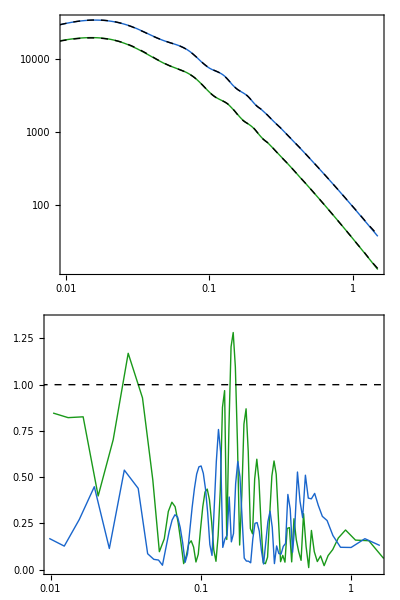

```mathematica
LogLogPlot[{PGA[k,hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,A0GAinf]*Pmax[k,hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,σGAinf,λmax],PGA[k,hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,A0GAsup]*Pmax[k,hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,σGAsup,λmax],PRDinfPk[k],PRDsupPk[k]},{k,9*10^-3,1.5},PlotRange->{{0.01,1.5},All},PlotStyle->{Directive[RGBColor[0.1,0.6,0.1],Thick],Directive[RGBColor[0.1,0.4,0.8],Thick],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k~[h \\, \\text{Mpc}^{-1}]","P(k)~[(\\text{Mpc} \\, h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLabel->MaTeX["\\text{Edge-of-Box}",Magnification->1.5],PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Inferior}"],Style[MaTeX["\\text{Superior}",Magnification->1.5]]},LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{30,15}],{0.22,0.25}],ImageSize->420,AspectRatio->0.6,ImagePadding->{{85,5},{0,0}}]//Quiet;
ListLogLinearPlot[{MAPEGAinf[[31;;-1]],MAPEGAsup[[31;;-1]]},Joined->True,PlotRange->{{0.01,1.5},{0,1.35}},PlotStyle->{Directive[RGBColor[0.1,0.6,0.1],Thick],Directive[RGBColor[0.1,0.4,0.8],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k~[h \\, \\text{Mpc}^{-1}]","\\text{MAPE(\\text{GA})}"},BaseStyle->{FontFamily->"Times",FontSize->16},Epilog->{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]},ImageSize->420,AspectRatio->0.3,ImagePadding->{{85,5},{55,0}}]//Quiet;
PlotPaper=Column[{%%,%},Spacings->0]
```

```mathematica
Export["Edge_of_box.pdf",PlotPaper]
```

Edge_of_box.pdf

## Out-of-Box

## Inferior Limit

### Data

```mathematica
(* Data from CLASS *)
PRDinfData=Import["./Data/PRD_out_inf_pk.dat","Table"][[5;;-1]];
PRDinfPk=Interpolation[PRDinfData];
```

```mathematica
hPRDinf=0.61;
ωbPRDinf=0.02;
ΩbPRDinf=ωbPRDinf*hPRDinf^-2;
ωcPRDinf=0.1;
ωmPRDinf=ωbPRDinf+ωcPRDinf;
ΩmPRDinf=ωmPRDinf*hPRDinf^-2;
nsPRDinf=0.85;
AsPRDinf=1.0;
σ8PRDinf=0.487797;
```

### Compute Normalization

```mathematica
R8=8;            (* Mpc h^-1 *)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]); (* Top-hat Filter *)
IntegralGA:=NIntegrate[k^(nsPRDinf+2) Tnw[k,hPRDinf,ωbPRDinf,ωmPRDinf]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GAinf=2*π^2 σ8PRDinf^2/IntegralGA;
```

### Compute Correction

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λmax=0.1;
```

```mathematica
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, eq] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
(* Fix Subscript[λ, max] = 0.1 *)
DDP=D[D[PGA[k,hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,A0GAinf]*Pmax[k,hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,σmax,λmax],k],k]/.k->kmax[hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf]//Simplify;
σDDP=Solve[DDP==DDPkclass[hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,AsPRDinf],σmax]//Quiet
```

{{σmax→0.000526177-0.00521363 ⅈ},{σmax→0.000526177+0.00521363 ⅈ}}

```mathematica
σGAinf=Re[σDDP[[1,1,2]]]
```

0.000526177

### Accuracy

#### Genetic Algorithm

```mathematica
MAPEGAinf=Table[{PRDinfData[[j,1]],Abs[1-PGA[PRDinfData[[j,1]],hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,A0GAinf]/PRDinfData[[j,2]]*Pmax[PRDinfData[[j,1]],hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,σGAinf,λmax]]*100},{j,1,Length[PRDinfData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

0.489631

## Superior Limit

### Data

```mathematica
(* Data from CLASS *)
PRDsupData=Import["./Data/PRD_out_sup_pk.dat","Table"][[5;;-1]];
PRDsupPk=Interpolation[PRDsupData];
```

```mathematica
hPRDsup=0.8;
ωbPRDsup=0.025;
ΩbPRDsup=ωbPRDsup*hPRDinf^-2;
ωcPRDsup=0.15;
ωmPRDsup=ωbPRDsup+ωcPRDsup;
ΩmPRDsup=ωmPRDsup*hPRDsup^-2;
nsPRDsup=1.2;
AsPRDsup=2.8;
σ8PRDsup=1.24997;
```

### Compute Normalization

```mathematica
R8=8;            (* Mpc h^-1 *)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]); (* Top-hat Filter *)
IntegralGA:=NIntegrate[k^(nsPRDsup+2) Tnw[k,hPRDsup,ωbPRDsup,ωmPRDsup]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GAsup=2*π^2 σ8PRDsup^2/IntegralGA;
```

### Compute Correction

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λmax=0.1;
```

```mathematica
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, eq] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
(* Fix λ = 0.4 *)
DDP=D[D[PGA[k,hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,A0GAsup]*Pmax[k,hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,σ,λmax],k],k]/.k->kmax[hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup]//Simplify;
σDDP=Solve[DDP==DDPkclass[hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,AsPRDsup],σ]//Quiet
```

{{σ→-0.0109615},{σ→0.00368794}}

```mathematica
σGAsup=Re[σDDP[[2,1,2]]]
```

0.00368794

### Accuracy

#### Genetic Algorithm

```mathematica
MAPEGAsup=Table[{PRDsupData[[j,1]],Abs[1-PGA[PRDsupData[[j,1]],hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,A0GAsup]/PRDsupData[[j,2]]*Pmax[PRDsupData[[j,1]],hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,σGAsup,λmax]]*100},{j,1,Length[PRDsupData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

0.655693

## Paper Plot

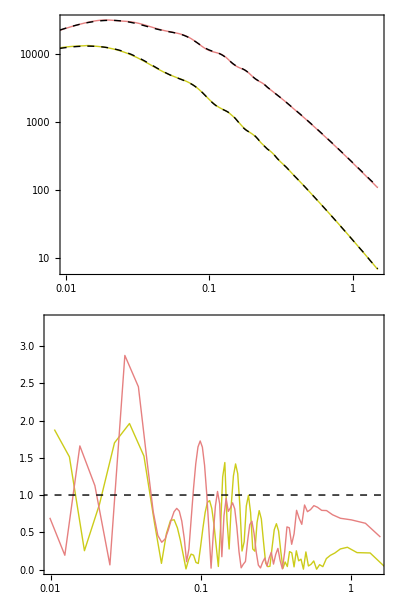

```mathematica
LogLogPlot[{PGA[k,hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,A0GAinf]*Pmax[k,hPRDinf,ωbPRDinf,ωmPRDinf,nsPRDinf,σGAinf,λmax],PGA[k,hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,A0GAsup]*Pmax[k,hPRDsup,ωbPRDsup,ωmPRDsup,nsPRDsup,σGAsup,λmax],PRDinfPk[k],PRDsupPk[k]},{k,9*10^-3,1.5},PlotRange->{{0.01,1.5},All},PlotStyle->{Directive[RGBColor[0.8,0.8,0.1],Thick],Directive[RGBColor[0.9,0.5,0.5],Thick],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k~[h \\, \\text{Mpc}^{-1}]","P(k)~[(\\text{Mpc} \\, h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLabel->MaTeX["\\text{Out-of-Box}",Magnification->1.5],PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Inferior}"],Style[MaTeX["\\text{Superior}",Magnification->1.5]]},LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{30,15}],{0.22,0.22}],ImageSize->420,AspectRatio->0.6,ImagePadding->{{85,5},{0,0}}]//Quiet;
ListLogLinearPlot[{MAPEGAinf[[31;;-1]],MAPEGAsup[[31;;-1]]},Joined->True,PlotRange->{{0.01,1.5},{0,3.35}},PlotStyle->{Directive[RGBColor[0.8,0.8,0.1],Thick],Directive[RGBColor[0.9,0.5,0.5],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k~[h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},Epilog->{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]},ImageSize->420,AspectRatio->0.3,ImagePadding->{{85,5},{55,0}}]//Quiet;
PlotPaper=Column[{%%,%},Spacings->0]
```

```mathematica
Export["Out_of_box.pdf",PlotPaper]
```

Out_of_box.pdf

## Fiducial

### Data

```mathematica
(* Data from CLASS *)
FidData=Import["./Data/fiducial_pk.dat","Table"][[5;;-1]];
```

```mathematica
a0B=0.51172;
a1B=0.04593;
a2B=0.73983;
a3B=1.56738;
a4B=1.16846;
a5B=0.59348;
a6B=0.19994;
a7B=25.09218;
a8B=9.36909;
a9B=0.00011;
σ8B[h_,Ωb_,Ωm_,ns_,As_]:=√As*(a0B*Ωm+a1B*h+a2B(Ωm-a3B*Ωb)(Log[a4B*Ωm]-a5B*ns)*(ns+a6B*h(a7B*Ωb-a8B*ns+Log[a9B*h])))
AsB[h_,Ωb_,Ωm_,ns_,σ8_]:=σ8^2*(a0B*Ωm+a1B*h+a2B(Ωm-a3B*Ωb)(Log[a4B*Ωm]-a5B*ns)*(ns+a6B*h(a7B*Ωb-a8B*ns+Log[a9B*h])))^-2
```

```mathematica
(* Parameters from Quijote *)
hFid=0.6711;
ΩbFid=0.049;
ωbFid=ΩbFid*hFid^2;
ΩmFid=0.3175;
ωmFid=ΩmFid*hFid^2;
nsFid=0.9624;
σ8Fid=0.834;
AsFid=AsB[hFid,ΩbFid,ΩmFid,nsFid,σ8Fid];(* Corresponding Subscript[A, s] *)
```

### Compute Normalization

```mathematica
R8=8;            (* Mpc h^-1 *)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]); (* Top-hat Filter *)
IntegralEH=NIntegrate[k^(nsFid+2) TEHnw[k*hFid,hFid,ωbFid,ωmFid]^2(WtopHat[R8*k])^2,{k,10^-5,10},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0EH=2*π^2 σ8Fid^2/IntegralEH;
IntegralGA:=NIntegrate[k^(nsFid+2) Tnw[k,hFid,ωbFid,ωmFid]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GA=2*π^2 σ8Fid^2/IntegralGA;
```

### Compute Correction

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λmax=0.4;
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, eq] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
(* Fix λ = 0.4 *)
DDP=D[D[PGA[k,hFid,ωbFid,ωmFid,nsFid,A0GA]*Pmax[k,hFid,ωbFid,ωmFid,nsFid,σmax,λmax],k],k]/.k->kmax[hFid,ωbFid,ωmFid,nsFid]//Simplify;
σDDP=Solve[DDP==DDPkclass[hFid,ωbFid,ωmFid,nsFid,AsFid],σmax]//Quiet
```

{{σmax→-0.0116892},{σmax→0.0158978}}

```mathematica
σGA=Re[σDDP[[1,1,2]]];
```

### Accuracy

#### Genetic Algorithm

```mathematica
MAPEGA=Table[{FidData[[j,1]],Abs[1-PGA[FidData[[j,1]],hFid,ωbFid,ωmFid,nsFid,A0GA]/FidData[[j,2]]*Pmax[FidData[[j,1]],hFid,ωbFid,ωmFid,nsFid,σGA,λmax]]*100},{j,1,Length[FidData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

0.319598

#### Eisenstein-Hu

```mathematica
MAPEEH=Table[{FidData[[j,1]],Abs[1-PEH[FidData[[j,1]],hFid,ωbFid,ωmFid,nsFid,A0EH]/FidData[[j,2]]]*100},{j,1,Length[FidData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

2.18605

#### Operon

```mathematica
MAPEOpe=Table[{FidData[[j,1]],Abs[1-FB[FidData[[j,1]],hFid,ΩbFid,ΩmFid]/FidData[[j,2]] PEHnw[FidData[[j,1]],hFid,ωbFid,ωmFid,nsFid,A0EH]]*100},{j,1,Length[FidData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

0.163745

### Comparison

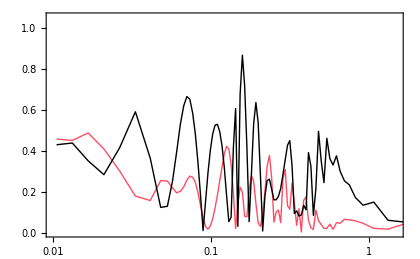

```mathematica
ListLogLinearPlot[{MAPEOpe[[31;;-1]],MAPEGA[[31;;-1]]},Joined->True,PlotRange->{{0.01,1.5},{0,1.05}},PlotStyle->{Directive[RGBColor[1,0.3,0.4],Thick],Directive[Black,Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k~[h \\, \\text{Mpc}^{-1}]","\\text{MAPE}"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Ce Sui et al}"],Style[MaTeX["\\text{GA}",Magnification->1.5]]},LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{30,15}],{0.22,0.815}],ImageSize->420]//Quiet
```

# Nonlinear Power Spectrum

```mathematica
Quit[]
```

### Packages

```mathematica
(* Package for plotting with LaTeX fonts *)
<<MaTeX`
LaunchKernels[];
SetDirectory[NotebookDirectory[]];
$ProcessorCount
$KernelCount
```

32

32

### Data

```mathematica
Import["./Data/cosmo_params.txt","Table"][[1]]
Params=Import["./Data/cosmo_params.txt","Table"][[2;;101]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
(* 100 spectra from a Latin-Hypercube of {h, Subscript[ω, b], Subscript[ω, m], Subscript[n, s], 10^9 Subscript[A, s], Subscript[σ, 8]} *)
dir="./Data/spectra_halofit/";
paths=FileNameJoin[{dir,"pnl"<>IntegerString[#,10,2]<>"_pk_nl.dat"}]&/@Range[0,99];
PkData=Rest[Import[#,"Data"][[4;;-1]]]&/@paths;
Pknl=ParallelTable[Interpolation[PkData[[i]],Method->"Spline"],{i,1,Length[PkData]}];
```

### Genetic Algorithm

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
AS2=0.00837;
kS2=0.081;
σS2=0.0404;
AS3=0.012538;
kS3=0.14376;
σS3=0.007586;
AS4=0.0038985;
kS4=1.1791;
σS4=0.3;

q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)

fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]

PS2[k_]:=1+AS2*ⅇ^(-((k-kS2)/σS2)^2)
PS3[k_]:=1-AS3*ⅇ^(-((k-kS3)/σS3)^2)
PS4[k_]:=1-AS4*ⅇ^(-((k-kS4)/σS4)^2)

PGA[k_,h_,ωb_,ωm_,ns_,A0_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2*PS2[k]*PS3[k]*PS4[k]

kmax[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
Pkmax[h_,ωb_,ωm_,ns_,As_]:=(7080.944 As ⅇ^(-1.2303 ωb) h^2.081426)/(ns^1.49408 ωm^0.66927)
Rmax[h_,ωb_,ωm_,ns_]:=0.6461-0.0097 h^2+0.0307ns+7.1728ωb+0.0239/ωm
PGAmax[h_,ωb_,ωm_,ns_]:=(0.04682 ⅇ^(-8.611 ωb) ωm^1.0587)/(h^0.8998 ns^3.916)
DPGAmax[h_,ωb_,ωm_,ns_]:=-0.38598+0.005318h-0.00145 h^2+0.2277ns-0.086155 ns^2-1.86 ωb-28.6088 ωb^2+2.9997ωm-6.426 ωm^2
Bmax[h_,ωb_,ωm_,ns_]:=Rmax[h,ωb,ωm,ns]-1
Amax[h_,ωb_,ωm_,ns_,σmax_,λmax_]:=-(DPGAmax[h,ωb,ωm,ns]/PGAmax[h,ωb,ωm,ns])(1+Bmax[h,ωb,ωm,ns])-√(2/π)(λmax/σmax)Bmax[h,ωb,ωm,ns]
Pmax[k_,h_,ωb_,ωm_,ns_,σmax_,λmax_]:=1+(Amax[h,ωb,ωm,ns,σmax,λmax](k-kmax[h,ωb,ωm,ns])+Bmax[h,ωb,ωm,ns])ⅇ^(-1/2(k-kmax[h,ωb,ωm,ns])^2/σmax^2)(1+Erf[λmax*(k-kmax[h,ωb,ωm,ns])/(√2 σmax)])
```

### Compute Normalization

```mathematica
R8=8;            (* Mpc h^-1 *)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]); (* Top-hat Filter *)
σ8=Params[[All,6]];
ti=AbsoluteTime[];
IntegralGA[i_]:=NIntegrate[k^(Params[[i,4]]+2) Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GaussKronrodRule"},MaxRecursion->15,AccuracyGoal->6];
A0GA=ParallelTable[2*π^2 σ8[[i]]^2/IntegralGA[i],{i,1,Length[PkData]}];
tf=AbsoluteTime[];
Print["Time computing A_0: ",(tf-ti)*1000, " ms"]
```

Time computing A_0: 65.464 ms

### Compute Correction

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λmax=0.4;
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, eq] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
(* Fix Subscript[λ, max] = 0.4 *)
ti=AbsoluteTime[];
DDP=ParallelTable[D[D[PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pmax[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σmax,λmax],k],k]/.k->kmax[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]]],{i,1,Length[PkData]}]//Simplify;
σDDP=ParallelTable[Solve[DDP[[i]]==DDPkclass[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]]],σmax]//Quiet,{i,Length[PkData]}];
(* Take the smallest one in absolute value *)
MinAbsKeepSign[pair_]:=First@MinimalBy[pair,Abs]
σGA=MinAbsKeepSign/@Table[{Re[σDDP[[i]][[1,1,2]]],Re[σDDP[[i]][[2,1,2]]]},{i,1,Length[PkData]}];
tf=AbsoluteTime[];
Print["Time computing corrections: ",(tf-ti)*1000," ms"]
```

Time computing corrections: 201.03 ms

## HaloFIT

### P_full

```mathematica
(* Dimensionless MPS *)
ΔGA[k_,i_]:=k^3/(2 π^2)*PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pmax[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σGA[[i]],λmax]
```

```mathematica
(* 2-Halo term *)
ΔQ[k_,i_]:=ΔGA[k,i]((1+ΔGA[k,i])^βn[i]/(1+αn[i]*ΔGA[k,i]))ⅇ^(-f[k,i]);
(* 1-Halo term *)
ΔH[k_,i_]:=ΔHP[k,i]/(1+μn*y[k,i]^-1+10^log10νn[i]*y[k,i]^-2)
ΔHP[k_,i_]:=(10^log10an[i]*y[k,i]^(3*f1[i]))/(1+10^log10bn[i]*y[k,i]^f2[i]+(10^log10cn[i]*f3[i]*y[k,i])^(3-γn[i]))
f[k_,i_]:=y[k,i]/4+y[k,i]^2/8
y[k_,i_]:=k/kσ[[i]]
αn[i_]:=Abs[6.0835+1.3373*neff[[i]]-0.1959*neff[[i]]^2-5.5274*CH[[i]]];
βn[i_]:=2.0379-0.7354*neff[[i]]+0.3157*neff[[i]]^2+1.2490*neff[[i]]^3+0.3980*neff[[i]]^4-0.1682*CH[[i]];
log10an[i_]:=1.5222+2.8553*neff[[i]]+2.3706*neff[[i]]^2+0.9903*neff[[i]]^3+0.2250*neff[[i]]^4-0.6038*CH[[i]];
log10bn[i_]:=-0.5642+0.5864*neff[[i]]+0.5716*neff[[i]]^2-1.5474*CH[[i]];
log10cn[i_]:=0.3698+2.0404*neff[[i]]+0.8161*neff[[i]]^2+0.5869*CH[[i]];
γn[i_]:=0.1971-0.0843*neff[[i]]+0.8460*CH[[i]];
μn=0;
log10νn[i_]:=5.2105+3.6902*neff[[i]];
f1[i_]:=(Params[[i,3]]/Params[[i,1]]^2)^-0.0307;
f2[i_]:=(Params[[i,3]]/Params[[i,1]]^2)^-0.0585;
f3[i_]:=(Params[[i,3]]/Params[[i,1]]^2)^0.0743;
```

```mathematica
(* Non-linear scale Subscript[k, σ] *)
σ2[R_,i_]:=NIntegrate[ΔGA[k,i]/k*ⅇ^(-k^2*R^2),{k,10^-5,1.5},Method->"GaussKronrodRule",WorkingPrecision->10,AccuracyGoal->10,PrecisionGoal->10]
kσ=ParallelTable[R^-1/. FindRoot[σ2[R,i]==1,{R,2}]//Quiet,{i,Length[PkData]}];
Rσ=kσ^-1;
```

```mathematica
lnSigma2[R_,i_]:=Log[σ2[R,i]];
g[x_,i_]:=lnSigma2[Exp[x],i];
xσ=Log[Rσ];
g1[i_]:=(g[xσ[[i]]+ϵ,i]-g[xσ[[i]]-ϵ,i])/(2 ϵ);
(*Segunda derivada con Richardson*)
D1[i_]:=(g[xσ[[i]]+ϵ,i]-2 g[xσ[[i]],i]+g[xσ[[i]]-ϵ,i])/ϵ^2;
D2[i_]:=(g[xσ[[i]]+2ϵ,i]-2 g[xσ[[i]],i]+g[xσ[[i]]-2 ϵ,i])/(4 ϵ^2);
ϵ=10^-3;   (* step size *)
```

```mathematica
neff=ParallelTable[-3-g1[i]//Quiet ,{i,Length[PkData]}];
CH=ParallelTable[-(4/3 D1[i]-1/3 D2[i])//Quiet,{i,Length[PkData]}];
```

```mathematica
MAPEGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])*(2 π^2)/(PkData[[i]][[j,1]])^3(ΔQ[PkData[[i]][[j,1]],i]+ΔH[PkData[[i]][[j,1]],i])]},{j,Length[PkData[[i]]]}]//Quiet;
```

```mathematica
Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[PkData]}]//Quiet;
{Min[#],Max[#],Position[#,Min[#]][[1,1]],Position[#,Max[#]][[1,1]]}&@%
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@%%
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[PkData]}];
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[PkData]}];
```

{0.13866,0.858521,30,63}

{0.306189,0.282282,0.323411,0.448655}

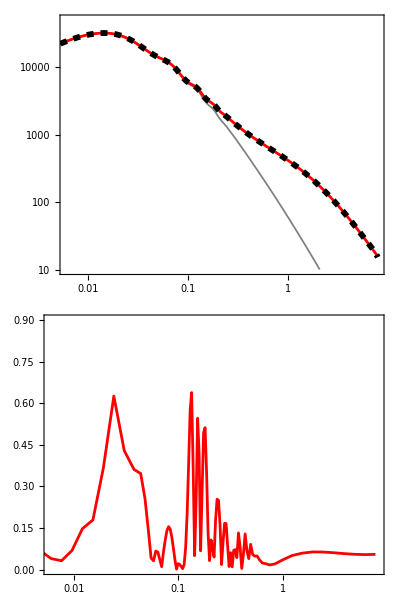

```mathematica
i=30;
LogLogPlot[{PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]],(2 π^2)/k^3(ΔQ[k,i]+ΔH[k,i]),Pknl[[i]][k]},{k,10^-3,8},PlotRange->{{0.006,8},{10,5*10^4}},PlotStyle->{Directive[Gray,Thickness[0.003]],Directive[Red],Directive[Black,Dashed,Thickness[0.01]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k) \\, [(\\text{Mpc}\\,h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{CLASS-L}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{GA}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{CLASS-NL}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{25,1}],
{0.24,0.345}],ImageSize->420,AspectRatio->0.6,ImagePadding->{{85,15},{0,10}}];
ListLogLinearPlot[MAPEGA[i],Joined->True,PlotRange->{{0.006,8},{0,0.9}},PlotStyle->{Directive[Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420,AspectRatio->0.3,ImagePadding->{{85,15},{50,0}}]//Quiet;
PlotPaper=Column[{%%,%},Spacings->0]
i=.;
```

```mathematica
Export["Halofit_Plot.pdf",PlotPaper]
```

Halofit_Plot.pdf

### P_GA P_(S,i)

```mathematica
(* Dimensionless MPS *)
ΔGA[k_,i_]:=k^3/(2 π^2)*PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]
```

```mathematica
(* 2-Halo term *)
ΔQ[k_,i_]:=ΔGA[k,i]((1+ΔGA[k,i])^βn[i]/(1+αn[i]*ΔGA[k,i]))ⅇ^(-f[k,i]);
(* 1-Halo term *)
ΔH[k_,i_]:=ΔHP[k,i]/(1+μn*y[k,i]^-1+10^log10νn[i]*y[k,i]^-2)
ΔHP[k_,i_]:=(10^log10an[i]*y[k,i]^(3*f1[i]))/(1+10^log10bn[i]*y[k,i]^f2[i]+(10^log10cn[i]*f3[i]*y[k,i])^(3-γn[i]))
f[k_,i_]:=y[k,i]/4+y[k,i]^2/8
y[k_,i_]:=k/kσ[[i]]
αn[i_]:=Abs[6.0835+1.3373*neff[[i]]-0.1959*neff[[i]]^2-5.5274*CH[[i]]];
βn[i_]:=2.0379-0.7354*neff[[i]]+0.3157*neff[[i]]^2+1.2490*neff[[i]]^3+0.3980*neff[[i]]^4-0.1682*CH[[i]];
log10an[i_]:=1.5222+2.8553*neff[[i]]+2.3706*neff[[i]]^2+0.9903*neff[[i]]^3+0.2250*neff[[i]]^4-0.6038*CH[[i]];
log10bn[i_]:=-0.5642+0.5864*neff[[i]]+0.5716*neff[[i]]^2-1.5474*CH[[i]];
log10cn[i_]:=0.3698+2.0404*neff[[i]]+0.8161*neff[[i]]^2+0.5869*CH[[i]];
γn[i_]:=0.1971-0.0843*neff[[i]]+0.8460*CH[[i]];
μn=0;
log10νn[i_]:=5.2105+3.6902*neff[[i]];
f1[i_]:=(Params[[i,3]]/Params[[i,1]]^2)^-0.0307;
f2[i_]:=(Params[[i,3]]/Params[[i,1]]^2)^-0.0585;
f3[i_]:=(Params[[i,3]]/Params[[i,1]]^2)^0.0743;
```

```mathematica
(* Non-linear scale Subscript[k, σ] *)
σ2[R_,i_]:=NIntegrate[ΔGA[k,i]/k*ⅇ^(-k^2*R^2),{k,10^-5,1.5},Method->"GaussKronrodRule",WorkingPrecision->10,AccuracyGoal->10,PrecisionGoal->10]
kσ=ParallelTable[R^-1/. FindRoot[σ2[R,i]==1,{R,2}]//Quiet,{i,Length[PkData]}];
Rσ=kσ^-1;
```

```mathematica
lnSigma2[R_,i_]:=Log[σ2[R,i]];
g[x_,i_]:=lnSigma2[Exp[x],i];
xσ=Log[Rσ];
g1[i_]:=(g[xσ[[i]]+ϵ,i]-g[xσ[[i]]-ϵ,i])/(2 ϵ);
(*Segunda derivada con Richardson*)
D1[i_]:=(g[xσ[[i]]+ϵ,i]-2 g[xσ[[i]],i]+g[xσ[[i]]-ϵ,i])/ϵ^2;
D2[i_]:=(g[xσ[[i]]+2ϵ,i]-2 g[xσ[[i]],i]+g[xσ[[i]]-2 ϵ,i])/(4 ϵ^2);
ϵ=10^-3;   (* step size *)
```

```mathematica
neff=ParallelTable[-3-g1[i]//Quiet ,{i,Length[PkData]}];
CH=ParallelTable[-(4/3 D1[i]-1/3 D2[i])//Quiet,{i,Length[PkData]}];
```

```mathematica
MAPEGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])*(2 π^2)/(PkData[[i]][[j,1]])^3(ΔQ[PkData[[i]][[j,1]],i]+ΔH[PkData[[i]][[j,1]],i])]},{j,Length[PkData[[i]]]}]//Quiet;
```

```mathematica
Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[PkData]}]//Quiet;
{Min[#],Max[#],Position[#,Min[#]][[1,1]],Position[#,Max[#]][[1,1]]}&@%
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@%%
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[PkData]}];
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[PkData]}];
```

{0.144772,0.916635,30,63}

{0.338038,0.328951,0.356838,0.497025}

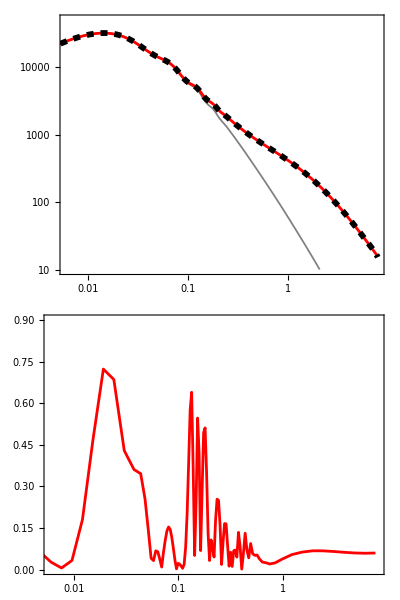

```mathematica
i=30;
LogLogPlot[{PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]],(2 π^2)/k^3(ΔQ[k,i]+ΔH[k,i]),Pknl[[i]][k]},{k,10^-3,8},PlotRange->{{0.006,8},{10,5*10^4}},PlotStyle->{Directive[Gray,Thickness[0.003]],Directive[Red],Directive[Black,Dashed,Thickness[0.01]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k) \\, [(\\text{Mpc}\\,h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{CLASS-L}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{GA}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{CLASS-NL}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{25,1}],
{0.24,0.345}],ImageSize->420,AspectRatio->0.6,ImagePadding->{{85,15},{0,10}}];
ListLogLinearPlot[MAPEGA[i],Joined->True,PlotRange->{{0.006,8},{0,0.9}},PlotStyle->{Directive[Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420,AspectRatio->0.3,ImagePadding->{{85,15},{50,0}}]//Quiet;
PlotPaper=Column[{%%,%},Spacings->0]
i=.;
```

#### P_GA

```mathematica
(* Dimensionless MPS *)
ΔGA[k_,i_]:=k^3/(2 π^2)*PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]/(PS2[k]*PS3[k]*PS4[k])
```

```mathematica
(* 2-Halo term *)
ΔQ[k_,i_]:=ΔGA[k,i]((1+ΔGA[k,i])^βn[i]/(1+αn[i]*ΔGA[k,i]))ⅇ^(-f[k,i]);
(* 1-Halo term *)
ΔH[k_,i_]:=ΔHP[k,i]/(1+μn*y[k,i]^-1+10^log10νn[i]*y[k,i]^-2)
ΔHP[k_,i_]:=(10^log10an[i]*y[k,i]^(3*f1[i]))/(1+10^log10bn[i]*y[k,i]^f2[i]+(10^log10cn[i]*f3[i]*y[k,i])^(3-γn[i]))
f[k_,i_]:=y[k,i]/4+y[k,i]^2/8
y[k_,i_]:=k/kσ[[i]]
αn[i_]:=Abs[6.0835+1.3373*neff[[i]]-0.1959*neff[[i]]^2-5.5274*CH[[i]]];
βn[i_]:=2.0379-0.7354*neff[[i]]+0.3157*neff[[i]]^2+1.2490*neff[[i]]^3+0.3980*neff[[i]]^4-0.1682*CH[[i]];
log10an[i_]:=1.5222+2.8553*neff[[i]]+2.3706*neff[[i]]^2+0.9903*neff[[i]]^3+0.2250*neff[[i]]^4-0.6038*CH[[i]];
log10bn[i_]:=-0.5642+0.5864*neff[[i]]+0.5716*neff[[i]]^2-1.5474*CH[[i]];
log10cn[i_]:=0.3698+2.0404*neff[[i]]+0.8161*neff[[i]]^2+0.5869*CH[[i]];
γn[i_]:=0.1971-0.0843*neff[[i]]+0.8460*CH[[i]];
μn=0;
log10νn[i_]:=5.2105+3.6902*neff[[i]];
f1[i_]:=(Params[[i,3]]/Params[[i,1]]^2)^-0.0307;
f2[i_]:=(Params[[i,3]]/Params[[i,1]]^2)^-0.0585;
f3[i_]:=(Params[[i,3]]/Params[[i,1]]^2)^0.0743;
```

```mathematica
(* Non-linear scale Subscript[k, σ] *)
σ2[R_,i_]:=NIntegrate[ΔGA[k,i]/k*ⅇ^(-k^2*R^2),{k,10^-5,1.5},Method->"GaussKronrodRule",WorkingPrecision->10,AccuracyGoal->10,PrecisionGoal->10]
kσ=ParallelTable[R^-1/. FindRoot[σ2[R,i]==1,{R,2}]//Quiet,{i,Length[PkData]}];
Rσ=kσ^-1;
```

```mathematica
lnSigma2[R_,i_]:=Log[σ2[R,i]];
g[x_,i_]:=lnSigma2[Exp[x],i];
xσ=Log[Rσ];
g1[i_]:=(g[xσ[[i]]+ϵ,i]-g[xσ[[i]]-ϵ,i])/(2 ϵ);
(*Segunda derivada con Richardson*)
D1[i_]:=(g[xσ[[i]]+ϵ,i]-2 g[xσ[[i]],i]+g[xσ[[i]]-ϵ,i])/ϵ^2;
D2[i_]:=(g[xσ[[i]]+2ϵ,i]-2 g[xσ[[i]],i]+g[xσ[[i]]-2 ϵ,i])/(4 ϵ^2);
ϵ=10^-3;   (* step size *)
```

```mathematica
neff=ParallelTable[-3-g1[i]//Quiet ,{i,Length[PkData]}];
CH=ParallelTable[-(4/3 D1[i]-1/3 D2[i])//Quiet,{i,Length[PkData]}];
```

```mathematica
MAPEGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])*(2 π^2)/(PkData[[i]][[j,1]])^3(ΔQ[PkData[[i]][[j,1]],i]+ΔH[PkData[[i]][[j,1]],i])]},{j,Length[PkData[[i]]]}]//Quiet;
```

```mathematica
Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[PkData]}]//Quiet;
{Min[#],Max[#],Position[#,Min[#]][[1,1]],Position[#,Max[#]][[1,1]]}&@%
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@%%
WorstFit=Position[#,Max[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[PkData]}];
BestFit=Position[#,Min[#]][[1,1]]&@Table[Mean[MAPEGA[i][[All,2]]],{i,1,Length[PkData]}];
```

{0.25589,0.820879,69,63}

{0.421441,0.408629,0.452873,0.547594}

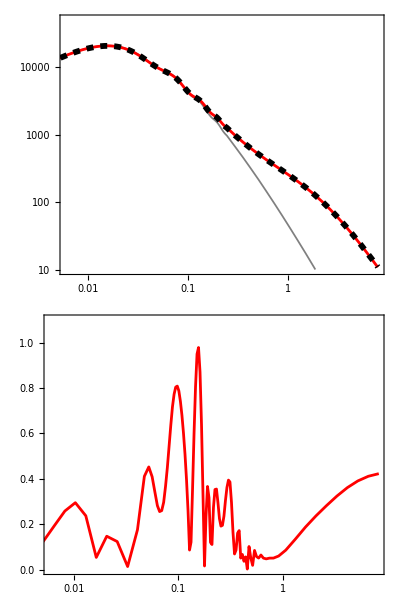

```mathematica
i=69;
LogLogPlot[{PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]],(2 π^2)/k^3(ΔQ[k,i]+ΔH[k,i]),Pknl[[i]][k]},{k,10^-3,8},PlotRange->{{0.006,8},{10,5*10^4}},PlotStyle->{Directive[Gray,Thickness[0.003]],Directive[Red],Directive[Black,Dashed,Thickness[0.01]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k) \\, [(\\text{Mpc}\\,h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{CLASS-L}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{GA}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{CLASS-NL}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->"Frame",LegendMarkerSize->{25,1}],
{0.24,0.345}],ImageSize->420,AspectRatio->0.6,ImagePadding->{{85,15},{0,10}}];
ListLogLinearPlot[MAPEGA[i],Joined->True,PlotRange->{{0.006,8},{0,1.1}},PlotStyle->{Directive[Red]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->420,AspectRatio->0.3,ImagePadding->{{85,15},{50,0}}]//Quiet;
PlotPaper=Column[{%%,%},Spacings->0]
i=.;
```